```mathematica
Integrate[DiracDelta[x],{x,0,1}]
```

HeavisideTheta[0]

```mathematica
Integrate[DiracDelta[x,y,z],{x,-1,1},{y,-1,1},{z,-1,1}]
```

1

```mathematica
Integrate[Sin[θ],{θ,0,π}]
```

2

```mathematica
Integrate[DiracDelta[r Sin[θ]Cos[ϕ],r Sin[θ]Sin[ϕ],r Cos[θ]] r^2 Sin[θ],{r,0,∞},{θ,0,π},{ϕ,0,2π}]
```

Integrate::idiv: Integral of r^2 DiracDelta[r Cos[θ],1+r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ]] Sin[θ] does not converge on {0,2 π}.

∫_0^∞ ∫_0^π ∫_0^(2 π) r^2 DiracDelta[r Cos[θ],1+r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ]] Sin[θ]ⅆϕⅆθⅆr

```mathematica
Integrate[DiracDelta[x],{x,-20,20}]
```

1

```mathematica
Integrate[DiracDelta[x^2-1]DiracDelta[x],{x,-20,20}]
```

∫_-20^20 DiracDelta[x] DiracDelta[-1+x^2]ⅆx

```mathematica
Integrate[(4π kk^2)/((2π)^3/V),{kk,0,(6 π^2 NN/V)^(1/3)}]
```

NN

```mathematica
Integrate[DiracDelta[x y]x,{x,-1,1},{y,-1,1}]
```

0

```mathematica
Integrate[DiracDelta[x y]x,{x,-1/2,1},{y,-1,1}]
```

1/2

```mathematica
Integrate[Integrate[DiracDelta[x y]x,{x,-1/2,1}],{y,-1/2,1}]
```

0

```mathematica
Integrate[Integrate[DiracDelta[x y]x,{y,-1/2,1}],{x,-1/2,1}]
```

1/2

```mathematica
√(2π)FourierTransform[e^2/r,r,q]
```

ⅈ e^2 π Sign[q]

```mathematica
1/(2π)FourierTransform[Exp[I q r Cos[θ]]
```

```mathematica
Clear[k];
Integrate[2π ω^2/k^2 1/cs^3(m/(2π))^2((4π Z α)/((ω/cs)^2+λ^2))^2 3/(4π M cs)(1)ni ω,{ω,0,ωD},Assumptions->{T>0,λ>0,cs>0,ωD>0}]//FullSimplify
```

-(3 m^2 ni Z^2 α^2 (ωD^2+(cs^2 λ^2+ωD^2) (2 Log[cs λ]-Log[cs^2 λ^2+ωD^2])))/(k^2 M (cs^2 λ^2+ωD^2))

```mathematica
-(3 m^2 ni Z^2 α^2)/(k^2 M)(ωD^2/(cs^2 λ^2+ωD^2)+ Log[(cs^2 λ^2)/(cs^2 λ^2+ωD^2)])
```

```mathematica
(ωD^2/(cs^2 λ^2+ωD^2)+ Log[(cs^2 λ^2)/(cs^2 λ^2+ωD^2)])//.{ωD->(6 π^2 ni)^(1/3),ni->1.,cs->10^-2,m->.5,Z->6,λ->(π/(4α f √(f^2+m^2)))^(1/2),f->(3π ne)^(1/3),ne->Z ni,M->10^4,T->10^-3,α->1/137.}
```

-8.95131

```mathematica
-(3 m^2 ni Z^2 α^2)/(k^2 M)(ωD^2/(cs^2 λ^2+ωD^2)+ Log[(cs^2 λ^2)/(cs^2 λ^2+ωD^2)])//.{ωD->(6 π^2 ni)^(1/3),ni->1.,cs->10^-2,m->.5,Z->6,λ->(π/(4α f √(f^2+m^2)))^(1/2),f->(3π ne)^(1/3),ne->Z ni,M->10^4,T->10^-3,α->1/137.}
```

(1.28768×10^-6)/k^2

```mathematica
%*5*10^10
```

64384.2/k^2

```mathematica
UnitConvert[Quantity[10^-5,"Centimeters"] ℏ^-1 c^-1/.{ℏ->Quantity[1.,"ReducedPlanckConstant"],c->Quantity[1.,"SpeedOfLight"]}//UnitConvert,("Megaelectronvolts")^-1]
```

506773. /MeV

```mathematica
Solve[k==1/(√(1-β^2))me,β]
```

{{β→-(√(k^2-me^2))/k},{β→(√(k^2-me^2))/k}}

```mathematica
Solve[k==1/(√(1-β^2))me β,β]
```

{{β→-k/(√(k^2+me^2))},{β→k/(√(k^2+me^2))}}

```mathematica
Quantity[1,("Megaelectronvolts")^2]/(Quantity[1.,"Megaelectronvolts"]/Quantity[10^-5,"Centimeters"])ℏ^-1 c^-1/.{ℏ->Quantity[1.,"ReducedPlanckConstant"],c->Quantity[1.,"SpeedOfLight"]}//UnitConvert
```

506773.

```mathematica
Solve[48 π^2(m/k)^2==1,k]//N
```

{{k→-21.7656 m},{k→21.7656 m}}

```mathematica
ωD//.{ωD->(6 π^2 ni)^(1/3),ni->1,cs->10^-2,m->.5,Z->6,λ->(π/(4 e^2 f √(f^2+m^2)))^(1/2),f->(3 π^2 ne)^(1/3),ne->Z ni,M->10^4,T->10^-3}//N
```

3.89778

```mathematica
λ//.{ωD->(6 π^2 ni)^(1/3),ni->1,cs->10^-2,m->.5,Z->6,λ->(π/(4α f √(f^2+m^2)))^(1/2),f->(3 π^2 ne)^(1/3),ne->Z ni,M->10^4,T->10^-3,α->1/137}
```

1.84159

```mathematica
-(3 α^2 m^2 ni Z^2)/(k^2 M)(1+Log[(cs^2 λ^2)/(cs^2 λ^2+ωD^2)])//.{ωD->(6 π^2 ni)^(1/3),ni->1,cs->10^-2,m->.5,Z->6,λ->(π/(4α f √(f^2+m^2)))^(1/2),f->(3 π^2 ne)^(1/3),ne->Z ni,M->10^4,T->10^-3,α->1/137}
```

(1.39681×10^-6)/k^2

```mathematica
(1+ (2 Log[cs λ]-Log[ωD^2]))//.{ωD->(6 π^2 ni)^(1/3),ni->1,cs->10^-2,m->.5,Z->6,e->.3,λ->(π/(4 e^2 f √(f^2+m^2)))^(1/2),f->.5,M->10^4,T->10^-3}//N
```

-7.72505

```mathematica
(6 π^2 ni)^(1/3)/.ni->1
```

6^(1/3) π^(2/3)

```mathematica
%//N
```

3.89778

```mathematica
2π ω^2/k^2 1/cs^3(m/(2π))^2((4π Z e^2)/((ω/cs)^2+λ^2))^2 3/(2M cs)(1/(Exp[ω/T]-1)+1)ni ω//.{ni->1,cs->10^-2,m->.5,Z->6,e->.3,λ->(π/(4 e^2 f √(f^2+m^2)))^(1/2),f->.5,M->10^4,T->10^-3}
```

(27482.7 (1+1/(-1+ⅇ^(1000 ω))) ω^3)/(k^2 (24.6827+10000 ω^2)^2)

```mathematica
(27482.652533603512 (1+1/(-1+ⅇ^(1000 ω))) ω^3)/((24.682682989768697+10000 ω^2)^2)/.ω->3
```

0.0000915586

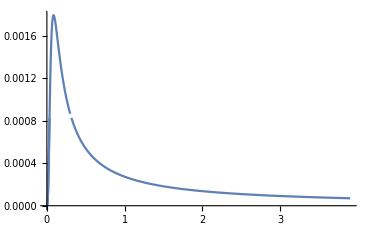

```mathematica
Show[Plot[(27482.652533603512 (1+1/(-1+ⅇ^(1000 ω))) ω^3)/((24.682682989768697+10000 ω^2)^2),{ω,0,.3}],Plot[(27482.652533603512 (1) ω^3)/((24.682682989768697+10000 ω^2)^2),{ω,0,6^(1/3) π^(2/3)}],PlotRange->All]
```

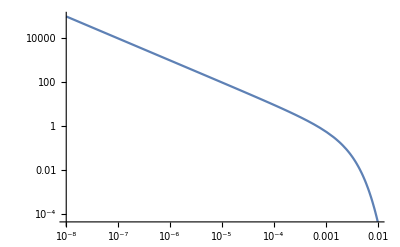

```mathematica
LogLogPlot[1/(-1+ⅇ^(1000 ω)),{ω,10^-8,10^-2},PlotRange->All]
```

```mathematica
Series[1/(-1+ⅇ^(1000 ω)),{ω,0,1}]
```

1/(1000 ω)-1/2+(250 ω)/3+O[ω]^2

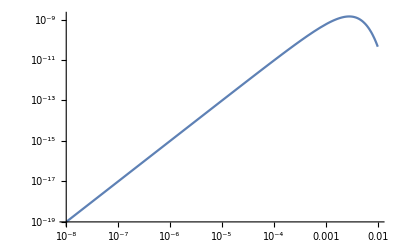

```mathematica
LogLogPlot[ω^3 1/(-1+ⅇ^(1000 ω)),{ω,10^-8,10^-2},PlotRange->All]
```

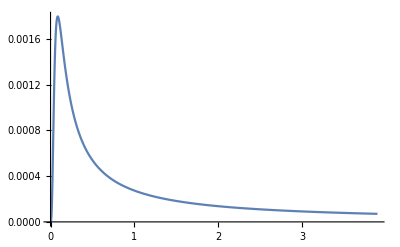

```mathematica
Plot[(27482.652533603512 (1) ω^3)/((24.682682989768697+10000 ω^2)^2),{ω,0,6^(1/3) π^(2/3)},PlotRange->All]
```

```mathematica
NIntegrate[(27482.652533603512 (1+1/(-1+ⅇ^(1000 ω))) ω^3)/((24.682682989768697+10000 ω^2)^2),{ω,0,6^(1/3) π^(2/3)}]
```

0.00106157

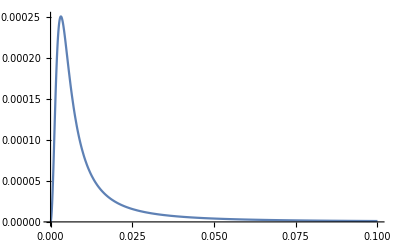

```mathematica
Plot[ω^2(1/((ω/cs)^2+.1))^2(1/(Exp[ω/T]-1)+1) ω/.{cs->10^-2,T->1},{ω,0,.1},PlotRange->All]
```

```mathematica
Plot[ω^2(1/((ω/cs)^2+1))^2(1/(Exp[ω/T]-1)) ω/.{cs->10^-2,T->1},{ω,0,.1},PlotRange->All]
```

```mathematica
(π/(4 e^2 f √(f^2+m^2)))^(1/2)/.{e->.3,f->.5,m->.5}
```

4.96817

```mathematica
Integrate[(4π k^2)/(2π)^3 Exp[I cs k t]/(cs k),{k,0,kD},Assumptions->{kD>0,cs>0,t>0}]//FullSimplify
```

(-1+ⅇ^(ⅈ cs kD t) (1-ⅈ cs kD t))/(2 cs^3 π^2 t^2)

```mathematica
Integrate[Exp[-I ω t]((-1+ⅇ^(ⅈ cs kD t) (1-ⅈ cs kD t))/(2 cs^3 π^2 t^2)),{t,-∞,∞},Assumptions->{kD>0,cs>0,ω>0}]
```

(ω-Abs[-cs kD+ω]+cs kD Sign[cs kD-ω])/(2 cs^3 π)

```mathematica
Integrate[Exp[-I ω t],{t,-∞,∞},Assumptions->{kD>0,cs>0,ω>0}]
```

Integrate::idiv: Integral of ⅇ^(-ⅈ t ω) does not converge on {-∞,∞}.

Integrate[ⅇ^(-ⅈ t ω),{t,-∞,∞},Assumptions→{kD>0,cs>0,ω>0}]

```mathematica
((-1+ⅇ^(ⅈ cs kD t) (1-ⅈ cs kD t))/(2 cs^3 π^2 t^2))^2//Expand
```

1/(4 cs^6 π^4 t^4)-ⅇ^(ⅈ cs kD t)/(2 cs^6 π^4 t^4)+ⅇ^(2 ⅈ cs kD t)/(4 cs^6 π^4 t^4)+(ⅈ ⅇ^(ⅈ cs kD t) kD)/(2 cs^5 π^4 t^3)-(ⅈ ⅇ^(2 ⅈ cs kD t) kD)/(2 cs^5 π^4 t^3)-(ⅇ^(2 ⅈ cs kD t) kD^2)/(4 cs^4 π^4 t^2)

```mathematica
Integrate[Exp[-I ω t]((-1+ⅇ^(ⅈ cs kD t) (1-ⅈ cs kD t))/(2 cs^3 π^2 t^2))^2,{t,-∞,∞},Assumptions->{kD>0,cs>0,ω>0}]
```

$Aborted

```mathematica
Integrate[Exp[-I ω t]((-1+ⅇ^(ⅈ cs kD t) (1-ⅈ cs kD t))/(2 cs^3 π^2 t^2))^2,{t,-∞,∞},Assumptions->{cs>0,kD>0,ω>0}]
```

$Aborted

```mathematica
(ω^3 (π-ⅈ Log[-ⅈ cs kD]+ⅈ Log[ⅈ cs kD]))/(24 cs^6 π^4)
```

```mathematica
(ω-Abs[-cs kD+ω]+cs kD Sign[cs kD-ω])/(2 cs^3 π)
```

```mathematica
ⅈ (Log[-1])
```

-π

```mathematica
(ω-Abs[-cs kD+ω]+cs kD Sign[cs kD-ω])/(2 cs^3 π)//FullSimplify
```

```mathematica
(ω-(-cs kD+ω)+cs kD (-1))/(2 cs^3 π)
```

0

```mathematica
{λ,ωD}//.{ωD->(6 π^2 ni)^(1/3),ni->1.,cs->10^-2,m->.5,Z->6,λ->(π/(4α f √(f^2+m^2)))^(1/2),f->(3π ne)^(1/3),ne->Z ni,M->10^4,T->10^-3,α->1/137.}
```

{2.69115,3.89778}

```mathematica
Log[(cs^2 λ^2)/(cs^2 λ^2+ωD^2)]//.{ωD->(6 π^2 ni)^(1/3),ni->1.,cs->10^-2,m->.5,Z->6,λ->(π/(4α f √(f^2+m^2)))^(1/2),f->(3π ne)^(1/3),ne->Z ni,M->10^4,T->10^-3,α->1/137.}
```

-9.95127

```mathematica
Log[(4 k^2)/λ^2]//.{ωD->(6 π^2 ni)^(1/3),ni->1.,cs->10^-2,m->.5,Z->6,λ->(π/(4α f √(f^2+m^2)))^(1/2),f->(3π ne)^(1/3),ne->Z ni,M->10^4,T->10^-3,α->1/137.}
```

Log[0.552313 k^2]

```mathematica
-(3 m^2 ni Z^2 α^2)/(k^2 M)(ωD^2/(cs^2 λ^2+ωD^2)+ Log[(cs^2 λ^2)/(cs^2 λ^2+ωD^2)])//.{ωD->(6 π^2 ni)^(1/3),ni->1.,cs->10^-2,m->.5,Z->6,λ->(π/(4α f √(f^2+m^2)))^(-1/2),f->(3 π^2 ne)^(1/3),ne->Z ni,M->10^4,α->1/137.}
```

(1.74818×10^-6)/k^2

```mathematica
%*5*10^5
```

0.874088/k^2

```mathematica
(3 m^2 ni Z^2 α^2)/(k^2 M)//.{ωD->(6 π^2 ni)^(1/3),ni->1.,cs->10^-2,m->.5,Z->6,λ->(π/(4α f √(f^2+m^2)))^(-1/2),f->(3 π^2 ne)^(1/3),ne->Z ni,M->10^4,α->1/137.}
```

(1.43854×10^-7)/k^2

```mathematica
%*5*10^5//FullSimplify
```

0.0719271/k^2

```mathematica
λ//.{ωD->(6 π^2 ni)^(1/3),ni->1.,cs->10^-2,m->.5,Z->6,λ->(π/(4α f √(f^2+m^2)))^(-1/2),f->(3 π^2 ne)^(1/3),ne->Z ni,M->10^4,α->1/137.}
```

0.54301

```mathematica
(Log[(4 k^2+λ^2)/λ^2]-(4 k^2)/(4 k^2+λ^2))
```

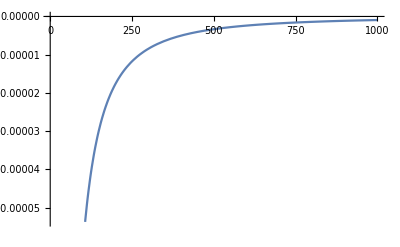

```mathematica
Plot[0.07192711385795728/(0.847860797775704+k^2)-(0.07192711385795728 Log[1.+1.1794388921193446 k^2])/k^2,{k,1,10^3}]
```

```mathematica
1/(6 π^2 ni)
```

```mathematica
V/(2π)^3/.{
```

```mathematica
Exp[I ω t](1/(Exp[ω/T] - 1)+1)+Exp[-I ω t](1/(Exp[ω/T]-1))//FullSimplify
```

Cos[t ω] Coth[ω/(2 T)]+ⅈ Sin[t ω]

```mathematica
1/(Exp[ω/T] - 1)Exp[-I ω t]//FullSimplify
```

ⅇ^(-ⅈ t ω)/(-1+ⅇ^(ω/T))

```mathematica
1/(-1+ⅇ^(-ω/T))+(1/(Exp[ω/T] - 1)+1)//FullSimplify
```

0

```mathematica
2 π (ω^2/k^2 1/cs^3)(m/(2 π))^2((4 π Z α)/((ω/cs)^2+λ^2))^2 3/(4 π M cs)
```

(6 m^2 Z^2 α^2 ω^2)/(cs^4 k^2 M (λ^2+ω^2/cs^2)^2)

```mathematica
% /. λ->0
```

(6 m^2 Z^2 α^2)/(k^2 M ω^2)

```mathematica
((3 m^2 Z^2 α^2 ω)/(2 π^2 cs^3 k^2 M ni))/((6 m^2 Z^2 α^2)/(k^2 M ω^2))
```

ω^3/(4 cs^3 ni π^2)

```mathematica
ω^3/(4 cs^3 ni π^2)//.{ω ->cs(6 π^2 ni)^(1/3),ni->1,cs->10^-2.}
```

1.5

```mathematica
Integrate[(6 m^2 Z^2 α^2)/(k^2 M (ω^2+cs^2 λ^2))ni ω,{ω,0,ωD},Assumptions->{cs>0,λ>0,ωD>0}]
```

(3 m^2 ni Z^2 α^2 Log[1+ωD^2/(cs^2 λ^2)])/(k^2 M)

```mathematica
(3 m^2 Z^2 α^2 ω)/(2 π^2 cs^3 k^2 M ni)
```

```mathematica
Integrate[(3 m^2 Z^2 α^2 ω)/(2 π^2 cs^3 k^2 M ni)ni ω,{ω,0,ωD},Assumptions->{cs>0,λ>0,ωD>0}]/.{ωD->cs(6 π^2 ni)^(1/3)}
```

(3 m^2 ni Z^2 α^2)/(k^2 M)

```mathematica
ωD//.{ωD->cs(6 π^2 ni)^(1/3),ni->1,cs->10^-2.}
```

0.0389778

```mathematica
(3/(4 π M cs))/(6/((2 π)^3 ni)(q^2 ω)/(2 M cs^3))
```

```mathematica
(2 cs^2 ni π^2)/(q^2 ω)//.{ω->ωD,ωD->cs(6 π^2 ni)^(1/3),ni->1,cs->10^-2.}
```

0.0506422/q^2

```mathematica
Integrate[1/((2 π Q^2 V^2)^(1/2))Exp[(-(ω-Q^2/(2 M))^2)/(2 Q^2 V^2)],{Q,0,∞},Assumptions->{ω>0,M>0,V > 0}]
```

(ⅇ^(ω/(2 M V^2)) BesselK[0,ω/(2 M V^2)])/(√(2 π) V)

```mathematica
Limit[1/((2 π Q^2 V^2)^(1/2))Exp[(-(ω-Q^2/(2 M))^2)/(2 Q^2 V^2)],V->0]
```

```mathematica
1/((2 π Q^2 V^2)^(1/2))Exp[(-(ω-Q^2/(2 M))^2)/(2 Q^2 V^2)]/.ω->x + Q^2/(2 M)
```

(ⅇ^(-x^2/(2 Q^2 V^2)))/(√(2 π) √(Q^2 V^2))

```mathematica
Integrate[(ⅇ^(-x^2/(2 ϵ^2)))/(√(2 π) ϵ),{x,-∞,∞},Assumptions->ϵ>0]
```

1

```mathematica
Series[γval,{T,0,1}]//FullSimplify
```

ⅇ^(-2/T) (1+ⅇ^(1/T)) O[T]^2+(1/2+O[T]^2)+Log[1-ⅇ^(-1/T)] (2 T+O[T]^2)

```mathematica
γval=1+T^2;
```

```mathematica
Integrate[u^3 Coth[u/(2T)],{u,0,1},Assumptions->T>0]
```

-1/4+2 ⅈ π T-(2 π^4 T^4)/15+2 T Log[-1+ⅇ^(1/T)]+6 T^2 PolyLog[2,ⅇ^(1/T)]-12 T^3 PolyLog[3,ⅇ^(1/T)]+12 T^4 PolyLog[4,ⅇ^(1/T)]

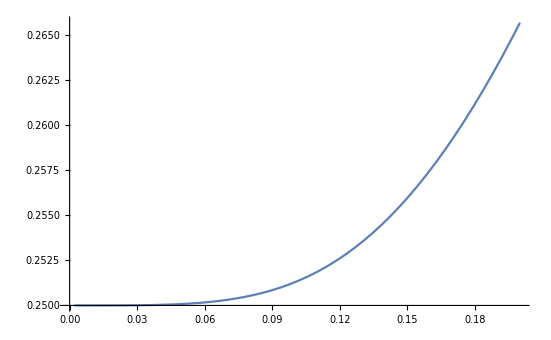

```mathematica
Plot[{-1/4+2 ⅈ π T-(2 π^4 T^4)/15+2 T Log[-1+ⅇ^(1/T)]+6 T^2 PolyLog[2,ⅇ^(1/T)]-12 T^3 PolyLog[3,ⅇ^(1/T)]+12 T^4 PolyLog[4,ⅇ^(1/T)],
},{T,0,.2}]
```

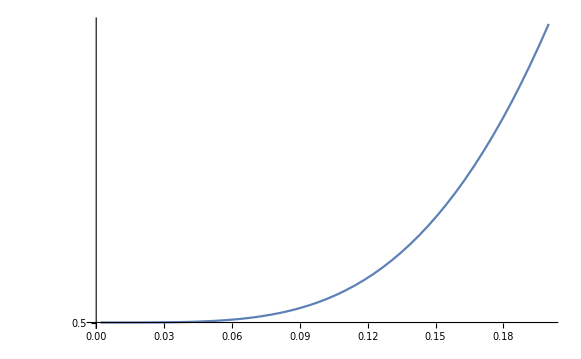

```mathematica
LogPlot[{2 ⅈ π T+2 T Log[-1+ⅇ^(1/T)]+6 T^2 PolyLog[2,ⅇ^(1/T)]-12 T^3 PolyLog[3,ⅇ^(1/T)]+12 T^4 PolyLog[4,ⅇ^(1/T)]},{T,0,.2}]
```

```mathematica
-1/4+2 ⅈ π T-(2 π^4 T^4)/15+2 T Log[-1+ⅇ^(1/T)]+6 T^2 PolyLog[2,ⅇ^(1/T)]-12 T^3 PolyLog[3,ⅇ^(1/T)]+12 T^4 PolyLog[4,ⅇ^(1/T)]
```

-1/4+2 ⅈ π T-(2 π^4 T^4)/15+2 T Log[-1+ⅇ^(1/T)]+6 T^2 PolyLog[2,ⅇ^(1/T)]-12 T^3 PolyLog[3,ⅇ^(1/T)]+12 T^4 PolyLog[4,ⅇ^(1/T)]

```mathematica
order=3;

ϵval=3/4 Integrate[u^3 Coth[u/(2T)],{u,0,1},Assumptions->T>0]//FullSimplify[#,T>0]&;
(*ϵval=1/4+T^2/2;*)
(*Series[ϵval ,{T,0,5},Assumptions->T>0];*)
(*ϵval=Normal@Series[ϵval ,{T,0,order},Assumptions->T>0]*)

γval=Integrate[3u Coth[u/(2T)],{u,0,1},Assumptions->T>0]//FullSimplify[#,T>0]&;
(*γval=3/2+π^2 T^2;*)
(*Series[γval ,{T,0,1},Assumptions->T>0];*)
(*γval=Normal@Series[γval ,{T,0,order},Assumptions->T>0]*)

Δval=√((4 ϵval)/(3 γval)-1/γval^2);
(*Series[Δval ,{T,0,1},Assumptions->T>0];*)
(*Δval=Normal@Series[Δval ,{T,0,order},Assumptions->T>0]*)

xval=u/Δval;
(*Series[xval ,{T,0,1},Assumptions->T>0];*)
(*xval=Normal@Series[xval ,{T,0,order},Assumptions->T>0]*)

yval=2 Q^2 γval Exp[-1/(2(Δval γval)^2)];
(*Series[yval ,{T,0,1},Assumptions->T>0];*)
(*yval=Normal@Series[yval ,{T,0,order},Assumptions->T>0]*)
```

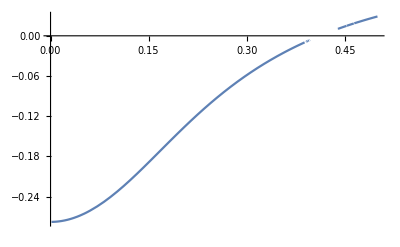

```mathematica
Plot[Evaluate[(4 ϵval)/(3 γval)-1/γval^2],{T,0,.5}]
```

```mathematica
Exp[-Q^2 T γval](1/Δval Exp[-u/(Δval^2 γval)]Sum[1/(p!√(2 π p))y^p Exp[-x^2/2 p],{p,2,100}])//.{y->yval,x->xval,T->.01,u->Q}/.Q->1
```

0.-1.25385×10^34 ⅈ

```mathematica
Δval/.T->.1
```

2.96261×10^-17+0.483831 ⅈ

```mathematica
Plot[Exp[-Q^2 T γval](1/Δval Exp[-u/(Δval^2 γval)]Sum[1/(p!√(2 π p))y^p Exp[-x^2/2 p],{p,2,100}])//.{y->yval,x->xval,T->.01,u->Q},{Q,0,3}]
```

-Graphics-

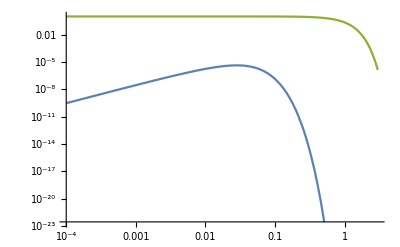

```mathematica
LogLogPlot[Evaluate[{Exp[-Q^2 T γval](Q^2((3 u^2)/u)(1/(Exp[u/T]-1))),Exp[-Q^2 T γval](1/Δval Exp[-u/(Δval^2 γval)]Sum[1/(p!√(2 π p))y^p Exp[-x^2/2 p],{p,2,100}]),
(*(ⅇ^(-((Q^2-u)^2)/(4 Q^2 T)))/(2 √π √(Q^2 T)),*)
Exp[-Q^2 γval]}//.{y->yval,x->xval,T->.01,u->Q}],{Q,.0001,3}]
```

```mathematica
1/((2 π Q^2 V^2)^(1/2))Exp[(-(ω-Q^2/(2 M))^2)/(2 Q^2 V^2)]//.{V->√(T/M),T->TT ωD,Q->QQ √(2 M ωD),ω->u ωD}//FullSimplify
```

(ⅇ^(-((QQ^2-u)^2)/(4 QQ^2 TT)))/(2 √π √(QQ^2 TT ωD^2))

```mathematica
1/(3((4 π)/3 kD^3))3 4 π Integrate[k^2((Cos[ω t]-1)/(ω Tanh[z/2])-I Sin[ω t]/ω)/.{ω->cs k},{k,0,kD},Assumptions->{t>0,z>0,cs >0}]//FullSimplify
```

1/(2 cs^3 kD^3 t^2)3 Csch[z/2] (-(2+cs^2 kD^2 t^2) Cosh[z/2]+2 (Cos[cs kD t+(ⅈ z)/2]+cs kD t Sin[cs kD t+(ⅈ z)/2]))

```mathematica
Integrate[Exp[-I ω t] 1/(2 cs^3 kD^3 t^2)3 Csch[z/2] (-(2+cs^2 kD^2 t^2) Cosh[z/2]+2 (Cos[cs kD t+(ⅈ z)/2]+cs kD t Sin[cs kD t+(ⅈ z)/2])),{t,-∞,∞},Assumptions->{ω>0,cs > 0,kD>0,z >0}]
```

Integrate::idiv: Integral of -(3 ⅇ^(-ⅈ t ω) Coth[z/2])/(2 cs kD)-(3 ⅇ^(-ⅈ t ω) Coth[z/2])/(cs^3 kD^3 t^2)+(3 ⅇ^(-ⅈ t ω) Cos[cs kD t+(ⅈ z)/2] Csch[z/2])/(cs^3 kD^3 t^2)+(3 ⅇ^(-ⅈ t ω) Csch[z/2] Sin[cs kD t+(ⅈ z)/2])/(cs^2 kD^2 t) does not converge on {-∞,∞}.

Integrate[1/(2 cs^3 kD^3 t^2)3 ⅇ^(-ⅈ t ω) Csch[z/2] ((-2-cs^2 kD^2 t^2) Cosh[z/2]+2 (Cos[cs kD t+(ⅈ z)/2]+cs kD t Sin[cs kD t+(ⅈ z)/2])),{t,-∞,∞},Assumptions→{ω>0,cs>0,kD>0,z>0}]

```mathematica
Integrate[Exp[-I ω t]((Cos[ω t]-1)/(ω Tanh[z/2])-I Sin[ω t]/ω),{t,-∞,∞},Assumptions->{ω>0,z>0}]
```

Integrate::idiv: Integral of -(ⅇ^(-ⅈ t ω) Coth[z/2])/ω+(ⅇ^(-ⅈ t ω) Cos[t ω] Coth[z/2])/ω-(ⅈ ⅇ^(-ⅈ t ω) Sin[t ω])/ω does not converge on {-∞,∞}.

Integrate[ⅇ^(-ⅈ t ω) (((-1+Cos[t ω]) Coth[z/2])/ω-(ⅈ Sin[t ω])/ω),{t,-∞,∞},Assumptions→{ω>0,z>0}]

```mathematica
-1/(2(Δ γ)^2)/.{Δ->√((4 ϵ)/(3 γ)-1/γ^2)}//FullSimplify
```

3/(6-8 γ ϵ)

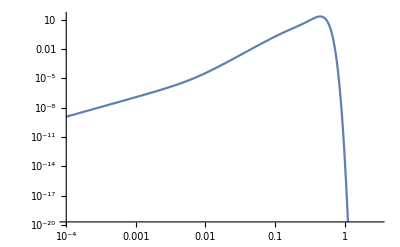

```mathematica
LogLogPlot[Evaluate[Exp[-Q^2 γval](Q^2(3 u)(1/(Exp[u/T]-1))+1/Δval Exp[-u/(Δval^2 γval)]Sum[1/(p!√(2 π p))y^p Exp[-x^2/2 p],{p,2,400}])//.{y->yval,x->xval,T->.04,u->Q}],{Q,.0001,3}]
```

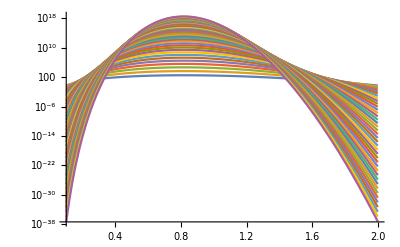

```mathematica
LogPlot[Evaluate[Table[1/(p!√(2 π p))y^p Exp[-x^2/2 p]//.{y->yval,x->xval,T->.02,u->Q},{p,2,40}]],{Q,.1,2}]
```

```mathematica
Series[ % ,{T,0,1},Assumptions->T>0]
```

2/(3 T)+T/30+O[T]^2

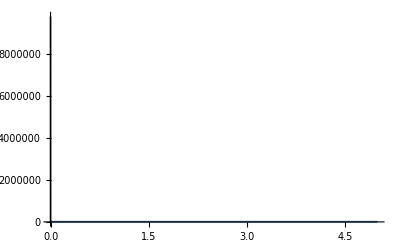

```mathematica
Plot[Coth[x],{x,0,5},PlotRange->All]
```

```mathematica
Series[(Cos[u ωl t]-1)Coth[(ωl u)/(2 T)]+I Sin[u ωl t],{t,0,2}]
```

ⅈ u ωl t-1/2 (u^2 ωl^2 Coth[(u ωl)/(2 T)]) t^2+O[t]^3

```mathematica
Integrate[Exp[-I ω t]Exp[-a t^2],{t,-∞,∞},Assumptions->{ω>0,r >0}]
```

ConditionalExpression[(ⅇ^(-ω^2/(4 a)) √π)/(√a),Re[a]>0]

```mathematica
Exp[I ω t](n+1)+Exp[-I ω t]n/. n->1/(Exp[ω/T]-1)//FullSimplify
```

Cos[t ω] Coth[ω/(2 T)]+ⅈ Sin[t ω]

```mathematica
Series[3/2+π^2 T^2+6 T Log[1-ⅇ^(-1/T)]-6 T^2 PolyLog[2,ⅇ^(-1/T)],{T,0,3}]
```

ⅇ^(-4/T) (ⅇ^(3/T) (-6 T^2+O[T]^4)+ⅇ^(2/T) (-(3 T^2)/2+O[T]^4)+ⅇ^(1/T) (-(2 T^2)/3+O[T]^4)+(-(3 T^2)/8+O[T]^4)+ⅇ^(4/T) Log[1-ⅇ^(-1/T)] (6 T+O[T]^4)+ⅇ^(4/T) (3/2+π^2 T^2+O[T]^4))

```mathematica
Integrate[(3 u^2)/u Coth[u/(2 T)],{u,0,1},Assumptions->T>0]
```

3/2+π^2 T^2+6 T Log[1-ⅇ^(-1/T)]-6 T^2 PolyLog[2,ⅇ^(-1/T)]

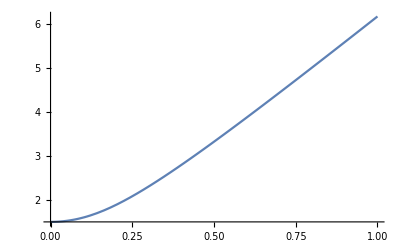

```mathematica
Plot[3/2+π^2 T^2+6 T Log[1-ⅇ^(-1/T)]-6 T^2 PolyLog[2,ⅇ^(-1/T)],{T,0,1}]
```

```mathematica
Integrate[Z n/. {Z->3 u^2,n->1/(Exp[u/T]-1)},{u,-1,1},Assumptions->T>0]
```

-1

```mathematica
Integrate[u/2 Z n/. {Z->3 u^2,n->1/(Exp[u/T]-1)},{u,-1,1},Assumptions->T>0]//FullSimplify[#,Assumptions->T>0]&
```

-3/8+3 ⅈ π T-(π^4 T^4)/5+3 T Log[-1+ⅇ^(1/T)]+9 T^2 (PolyLog[2,ⅇ^(1/T)]+2 T (-PolyLog[3,ⅇ^(1/T)]+T PolyLog[4,ⅇ^(1/T)]))

```mathematica
-3/8+3 ⅈ π T-(π^4 T^4)/5+3 T Log[-1+ⅇ^(1/T)]+9 T^2 (PolyLog[2,ⅇ^(1/T)]+2 T (-PolyLog[3,ⅇ^(1/T)]+T PolyLog[4,ⅇ^(1/T)]))/.T->.23
```

0.410867-1.33227×10^-15 ⅈ

```mathematica
Integrate[u/2 Z n/. {Z->3 u^2,n->1/(Exp[u/T]-1)}/.T->.23,{u,-1,1},Assumptions->T>0]
```

0.410867

```mathematica
Integrate[u/2 Z n/. {Z->3 u^2,n->1/(Exp[u/T]-1)},{u,-1,1},Assumptions->T>0]//FullSimplify[#,Assumptions->T>0]&
```

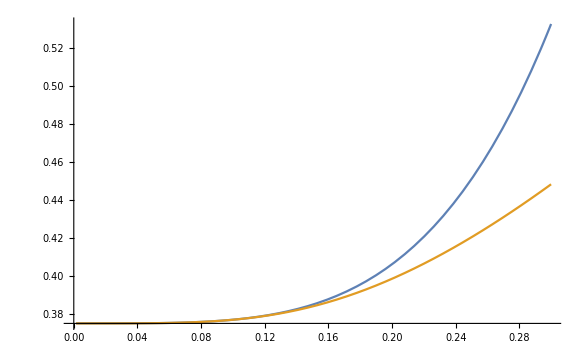

```mathematica
Plot[{3/8+π^4/5 T^4,-3/8+3 ⅈ π T-(π^4 T^4)/5+3 T Log[-1+ⅇ^(1/T)]+9 T^2 (PolyLog[2,ⅇ^(1/T)]+2 T (-PolyLog[3,ⅇ^(1/T)]+T PolyLog[4,ⅇ^(1/T)]))},{T,0,.3}]
```

```mathematica
Limit[-3/8+3 ⅈ π T-(π^4 T^4)/5+3 T Log[-1+ⅇ^(1/T)]+9 T^2 (PolyLog[2,ⅇ^(1/T)]+2 T (-PolyLog[3,ⅇ^(1/T)]+T PolyLog[4,ⅇ^(1/T)])),T->0]
```

3/8

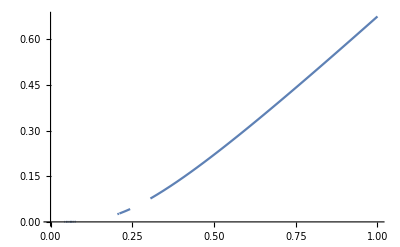

```mathematica
Plot[{-3/8+3 ⅈ π T-(π^4 T^4)/5+3 T Log[-1+ⅇ^(1/T)]+9 T^2 (PolyLog[2,ⅇ^(1/T)]+2 T (-PolyLog[3,ⅇ^(1/T)]+T PolyLog[4,ⅇ^(1/T)]))-3/8},{T,0,1}]
```

```mathematica
Limit[1/T(-3/8+3 ⅈ π T-(π^4 T^4)/5+3 T Log[-1+ⅇ^(1/T)]+9 T^2 (PolyLog[2,ⅇ^(1/T)]+2 T (-PolyLog[3,ⅇ^(1/T)]+T PolyLog[4,ⅇ^(1/T)]))-3/8),T->0]
```

0

```mathematica
Limit[1/T^2(-3/8+3 ⅈ π T-(π^4 T^4)/5+3 T Log[-1+ⅇ^(1/T)]+9 T^2 (PolyLog[2,ⅇ^(1/T)]+2 T (-PolyLog[3,ⅇ^(1/T)]+T PolyLog[4,ⅇ^(1/T)]))-3/8),T->0]
```

0

```mathematica
Limit[1/T^3(-3/8+3 ⅈ π T-(π^4 T^4)/5+3 T Log[-1+ⅇ^(1/T)]+9 T^2 (PolyLog[2,ⅇ^(1/T)]+2 T (-PolyLog[3,ⅇ^(1/T)]+T PolyLog[4,ⅇ^(1/T)]))-3/8),T->0]
```

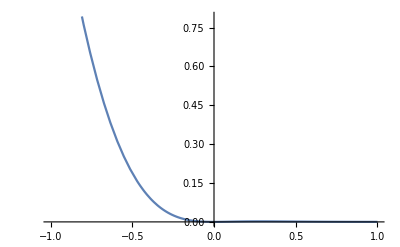

```mathematica
Plot[u/2 Z n/. {Z->3 u^2,n->1/(Exp[u/T]-1)}/. T->.1,{u,-1,1}]
```

```mathematica
Series[Evaluate[u/2 Z n/. {Z->3 u^2,n->1/(Exp[u/T]-1)}],{T,ϵ,3}]
```

(3 u^3)/(2 (-1+ⅇ^(u/ϵ)))+(3 ⅇ^(u/ϵ) u^4 (T-ϵ))/(2 (-1+ⅇ^(u/ϵ))^2 ϵ^2)+(3 ⅇ^(u/ϵ) u^4 (u+ⅇ^(u/ϵ) u+2 ϵ-2 ⅇ^(u/ϵ) ϵ) (T-ϵ)^2)/(4 (-1+ⅇ^(u/ϵ))^3 ϵ^4)+(ⅇ^(u/ϵ) u^4 (u^2+4 ⅇ^(u/ϵ) u^2+ⅇ^((2 u)/ϵ) u^2+6 u ϵ-6 ⅇ^((2 u)/ϵ) u ϵ+6 ϵ^2-12 ⅇ^(u/ϵ) ϵ^2+6 ⅇ^((2 u)/ϵ) ϵ^2) (T-ϵ)^3)/(4 (-1+ⅇ^(u/ϵ))^4 ϵ^6)+O[T-ϵ]^4

```mathematica
Limit[{(3 u^3)/(2 (-1+ⅇ^(u/ϵ))),(3 ⅇ^(u/ϵ) u^4 (T-ϵ))/(2 (-1+ⅇ^(u/ϵ))^2 ϵ^2),(3 ⅇ^(u/ϵ) u^4 (u+ⅇ^(u/ϵ) u+2 ϵ-2 ⅇ^(u/ϵ) ϵ) (T-ϵ)^2)/(4 (-1+ⅇ^(u/ϵ))^3 ϵ^4),(ⅇ^(u/ϵ) u^4 (u^2+4 ⅇ^(u/ϵ) u^2+ⅇ^((2 u)/ϵ) u^2+6 u ϵ-6 ⅇ^((2 u)/ϵ) u ϵ+6 ϵ^2-12 ⅇ^(u/ϵ) ϵ^2+6 ⅇ^((2 u)/ϵ) ϵ^2) (T-ϵ)^3)/(4 (-1+ⅇ^(u/ϵ))^4 ϵ^6)},ϵ->0,Assumptions->u<0]
```

{-(3 u^3)/2,0,0,0}

```mathematica
u/2 Z n//. {Z->3 u^2,n->1/(Exp[u/T]-1),u->T z}
3/2 T^4 Integrate[z^3/(-1+ⅇ^z),{z,-1/T,1/T},Assumptions->T>0]//FullSimplify[#,Assumptions->T>0]&
```

(3 T^3 z^3)/(2 (-1+ⅇ^z))

```mathematica
u/2 Z n/. {Z->3 u^2,n->1/(Exp[u/T]-1)}
```

(3 u^3)/(2 (-1+ⅇ^(u/T)))

```mathematica
Integrate[(3 u^3)/2 Coth[u/(2 T)],{u,0,1},Assumptions->T>0]
```

-3/8+3 ⅈ π T-(π^4 T^4)/5+3 T Log[-1+ⅇ^(1/T)]+9 T^2 PolyLog[2,ⅇ^(1/T)]-18 T^3 PolyLog[3,ⅇ^(1/T)]+18 T^4 PolyLog[4,ⅇ^(1/T)]

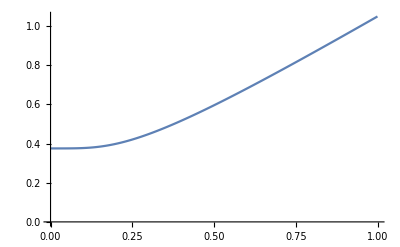

```mathematica
intresults=Table[{T,NIntegrate[(3 u^3)/(2 (-1+ⅇ^(u/T))),{u,-1,1}]},{T,0.00001,1,0.001}];
ListPlot[intresults,Joined->True]
```

```mathematica
func=Interpolation[intresults]
```

InterpolatingFunction[{{0.00001, 0.99901}}, <>]

```mathematica
func[0]-3/8
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

8.04246×10^-13

```mathematica
D[func[T],{T,5}]/.T->0.0001
```

0.

InterpolatingFunction::dmval: Input value {2.04286×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

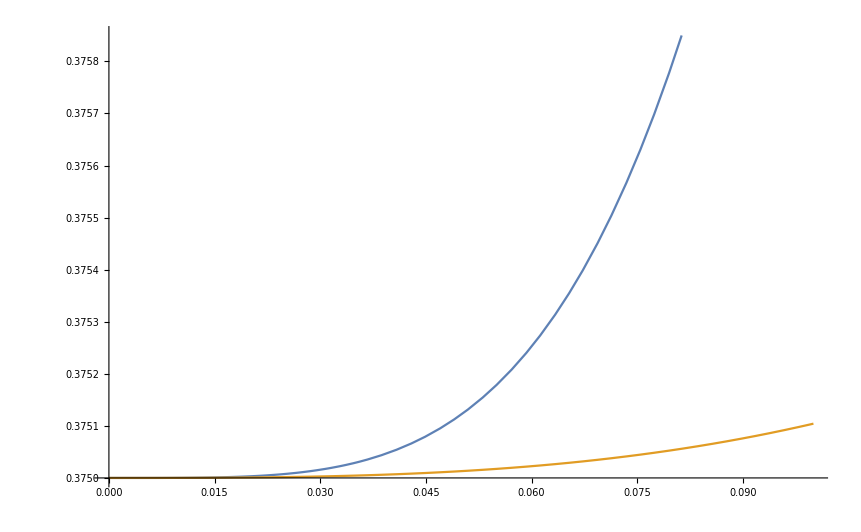

```mathematica
Plot[{func[T],3/8-(-0.000022855550785294554)T^2/(2!)+(0.62460953076382)T^3/(3!)},{T,0,.1}]
```

```mathematica
Integrate[(3 u)/(-1+ⅇ^(u/T)),{u,-1,1},Assumptions->T>0]
```

-3/2+6 ⅈ π T-π^2 T^2+6 T Log[-1+ⅇ^(1/T)]+6 T^2 PolyLog[2,ⅇ^(1/T)]

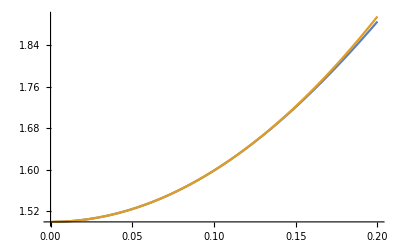

```mathematica
Plot[{-3/2+6 ⅈ π T-π^2 T^2+6 T Log[-1+ⅇ^(1/T)]+6 T^2 PolyLog[2,ⅇ^(1/T)],
3/2+π^2 T^2},{T,0,.2}]
```

```mathematica
Limit[-3/2+6 ⅈ π T-π^2 T^2+6 T Log[-1+ⅇ^(1/T)]+6 T^2 PolyLog[2,ⅇ^(1/T)],T->0]
```

3/2

```mathematica
Limit[1/T(-3/2+6 ⅈ π T-π^2 T^2+6 T Log[-1+ⅇ^(1/T)]+6 T^2 PolyLog[2,ⅇ^(1/T)]-3/2),T->0]
```

0

```mathematica
Limit[1/T^2(-3/2+6 ⅈ π T-π^2 T^2+6 T Log[-1+ⅇ^(1/T)]+6 T^2 PolyLog[2,ⅇ^(1/T)]-3/2),T->0]
```

π^2

```mathematica
Limit[1/T^6(-3/2+6 ⅈ π T-π^2 T^2+6 T Log[-1+ⅇ^(1/T)]+6 T^2 PolyLog[2,ⅇ^(1/T)]-(3/2+π^2 T^2)),T->0]
```

0

```mathematica
Integrate[Exp[-I u t]Exp[Q^2(α0-I t α1-t^2 α2)],{t,-∞,∞},Assumptions->{Q>0,α2>0}]
```

(ⅇ^(Q^2 α0-((u+Q^2 α1)^2)/(4 Q^2 α2)) √π)/(Q √α2)

```mathematica
(ⅇ^(Q^2 α0-((u+Q^2 α1)^2)/(4 Q^2 α2)) √π)/(Q √α2)//FullSimplify
```

(ⅇ^(Q^2 α0-((u+Q^2 α1)^2)/(4 Q^2 α2)) √π)/(Q √α2)

```mathematica
1/(-1+ⅇ^(u/T))-1/(-1+ⅇ^(-u/T))//FullSimplify
```

Coth[u/(2 T)]

```mathematica
Integrate[(3 u)/(-1+ⅇ^(u/T)),{u,-1,1},Assumptions->T>0]
```

-3/2+6 ⅈ π T-π^2 T^2+6 T Log[-1+ⅇ^(1/T)]+6 T^2 PolyLog[2,ⅇ^(1/T)]

```mathematica
Integrate[3 u Coth[u/(2 T)],{u,0,1},Assumptions->T >0]
```

3/2+π^2 T^2+6 T Log[1-ⅇ^(-1/T)]-6 T^2 PolyLog[2,ⅇ^(-1/T)]

-3/2+6 ⅈ π T-π^2 T^2+6 T Log[-1+ⅇ^(1/T)]+6 T^2 PolyLog[2,ⅇ^(1/T)]

```mathematica
-3/2+6 ⅈ π T-π^2 T^2+6 T Log[-1+ⅇ^(1/T)]+6 T^2 PolyLog[2,ⅇ^(1/T)]-(3/2+π^2 T^2+6 T Log[1-ⅇ^(-1/T)]-6 T^2 PolyLog[2,ⅇ^(-1/T)])//FullSimplify
```

-3-2 π T (-3 ⅈ+π T)-6 T Log[1-ⅇ^(-1/T)]+6 T Log[-1+ⅇ^(1/T)]+6 T^2 (PolyLog[2,ⅇ^(-1/T)]+PolyLog[2,ⅇ^(1/T)])

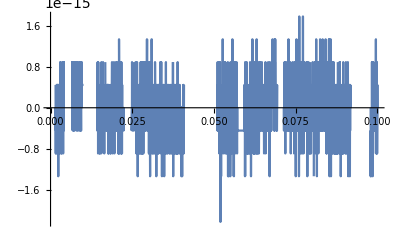

```mathematica
Plot[-3-2 π T (-3 ⅈ+π T)-6 T Log[1-ⅇ^(-1/T)]+6 T Log[-1+ⅇ^(1/T)]+6 T^2 (PolyLog[2,ⅇ^(-1/T)]+PolyLog[2,ⅇ^(1/T)]),{T,0,.1}]
```

```mathematica
Series[1/(ω √(4 π Q^2 α2))Exp[(-(u-Q^2)^2)/(4 Q^2 α2)],{Q,0,3}]
```

ⅇ^(-((-Q^2+u)^2)/(4 Q^2 α2)) (1/(2 √π √α2 ω Q)+O[Q]^4)

```mathematica
Limit[1/(ω √(4 π Q^2 α2))Exp[(-(u-Q^2)^2)/(4 Q^2 α2)],Q->0, Assumptions->{u>0,α2>0,ω>0}]
```

0

```mathematica
Integrate[Exp[-I u t]Exp[-I U t],{t,-∞,∞}]
```

Integrate::idiv: Integral of ⅇ^(-ⅈ t (u+U)) does not converge on {-∞,∞}.

∫_(-∞)^∞ ⅇ^(-ⅈ t u-ⅈ t U)ⅆt

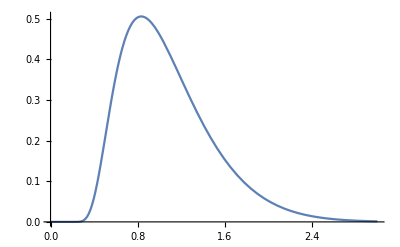

```mathematica
Plot[1/(ω √(4 π Q^2 α2))Exp[(-(u-Q^2)^2)/(4 Q^2 α2)]/.{ω->1,α2->3/8,u->1},{Q,0,3},PlotRange->All]
```

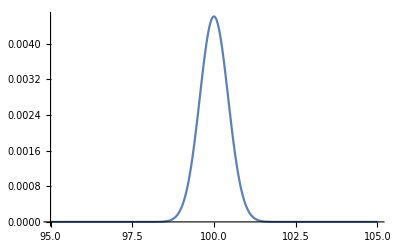

```mathematica
Plot[1/(ω √(4 π Q^2 α2))Exp[(-(u-Q^2)^2)/(4 Q^2 α2)]/.{ω->1,α2->3/8,u->10000},{Q,95,105},PlotRange->All]
```

```mathematica
Integrate[1/(√(4 π Q^2 α2))Exp[(-(u-Q^2)^2)/(4 Q^2 α2)],{Q,0,∞},Assumptions->{α2>0,u>0,ω>0}]
```

(ⅇ^(u/(2 α2)) BesselK[0,u/(2 α2)])/(2 √π √α2)

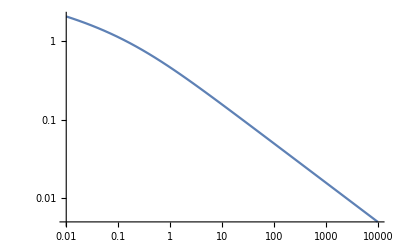

```mathematica
LogLogPlot[(ⅇ^(u/(2 α2)) BesselK[0,u/(2 α2)])/(2 √π √α2)/.{α2->3/8},{u,0.01,10000},PlotRange->All]
```

```mathematica
-1/(-1+ⅇ^(-u/T))//FullSimplify
```

1+1/(-1+ⅇ^(u/T))

```mathematica
Evaluate[{Exp[-2 Q^2 α0] 1/((2π)^3 ni)(q^2 ω)/(m cs^3)(1/(ⅇ^(ω/T)-1)+1),
1/(ωD √(4 π Q^2 α2))Exp[(-(u-Q^2)^2)/(4 Q^2 α2)]}
//.{α0->3/2,α2->3/8,Q->q^2/(2m ωD),u->ω/ωD,ωD->cs(6 π^2 ni)^(1/3),cs->.01,ni->1,m->10^4,T->.001}]
```

```mathematica
Plot3D[Evaluate[{Exp[-2 Q^2 α0] 1/((2π)^3 ni)(q^2 ω)/(m cs^3)(1/(ⅇ^(ω/T)-1)+1),
1/(ωD √(4 π Q^2 α2))Exp[(-(u-Q^2)^2)/(4 Q^2 α2)]}
//.{α0->3/2,α2->3/8,Q->q^2/(2m ωD),u->ω/ωD,ωD->cs(6 π^2 ni)^(1/3),cs->.01,ni->1,m->10^4,T->.001}],{ω,1,100},{q,1,100},AxesLabel->Automatic,PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[Evaluate[{Exp[-2 Q^2 α0] 1/((2π)^3 ni)(q^2 ω)/(m cs^3)(1/(ⅇ^(ω/T)-1)+1)}
//.{α0->3/2,α2->3/8,Q->q^2/(2m ωD),u->ω/ωD,ωD->cs(6 π^2 ni)^(1/3),cs->.01,ni->1,m->10^4,T->.001}],{ω,0,.04},{q,1,100},AxesLabel->Automatic,PlotRange->All]
```

-Graphics3D-

```mathematica
Manipulate[Plot[1/(ωD √(4 π Q^2 α2))Exp[(-(u-Q^2)^2)/(4 Q^2 α2)]//.{α0->3/2,α2->3/8,Q->q^2/(2m ωD),u->ω/ωD,ωD->cs(6 π^2 ni)^(1/3),cs->.01,ni->1,m->10^4,T->.001},{ω,0,1000},PlotRange->All],{q,0.1,400}]
```

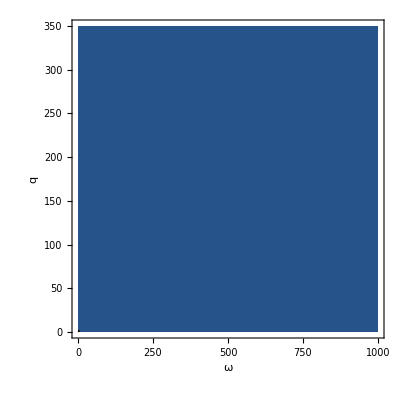

```mathematica
1[Evaluate[{1/(ωD √(4 π Q^2 α2))Exp[(-(u-Q^2)^2)/(4 Q^2 α2)]}
//.{α0->3/2,α2->3/8,Q->q^2/(2m ωD),u->ω/ωD,ωD->cs(6 π^2 ni)^(1/3),cs->.01,ni->1,m->10^4,T->.001}],{ω,0,1000},{q,.01,350},FrameLabel->{ω,q},PlotRange->All]
```

```mathematica
Manipulate[Plot[Evaluate[{√(π/(Q^2 α2))Exp[(-(u-Q^2)^2)/(4 Q^2 α2)]}//.{α0->3/2,α2->3/8,TT->.01}],{u,1,10000},PlotRange->All],{Q,.1,100}]
```

```mathematica
Manipulate[Plot[Evaluate[{Exp[-2 Q^2 α0] Q^2((3 u^2)/u)(1/(ⅇ^(u/TT)-1)+1)}//.{α0->3/2,α2->3/8,TT->.01}],{u,0,1},PlotRange->All],{Q,0.01,2}]
```

```mathematica
Manipulate[Plot[Evaluate[{Exp[-2 Q^2 α0] Q^2(3 u^2)/u(1/(ⅇ^(u/TT)-1)+1)HeavisideTheta[1-u]+√(π/(Q^2 α2))Exp[(-(u-Q^2)^2)/(4 Q^2 α2)]HeavisideTheta[u-1]}//.{α0->3/2,α2->3/8,TT->.01}],{u,0,100},PlotRange->{0,3}],{Q,0.01,10}]
```

```mathematica
Plot3D[Evaluate[{Exp[-2 Q^2 α0] Q^2(3 u^2)/u(1/(ⅇ^(u/TT)-1)+1)HeavisideTheta[1-u]+√(π/(Q^2 α2))Exp[(-(u-Q^2)^2)/(4 Q^2 α2)]HeavisideTheta[u-1]}//.{α0->3/2,α2->3/8,TT->.01}],{u,0,100},{Q,0.01,10},AxesLabel->Automatic]
```

-Graphics3D-

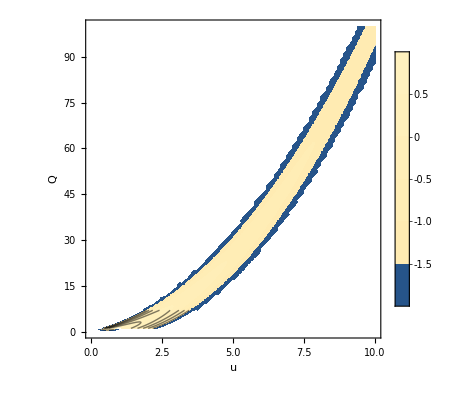

```mathematica
ContourPlot[Evaluate[{Log[Exp[-2 Q^2 α0] Q^2(3 u^2)/u(1/(ⅇ^(u/TT)-1)+1)HeavisideTheta[1-u]+√(π/(Q^2 α2))Exp[(-(u-Q^2)^2)/(4 Q^2 α2)]HeavisideTheta[u-1]]}//.{α0->3/2,α2->3/8,TT->.01}],{Q,0.01,10},{u,0,100},PlotRange->{-2,1},FrameLabel->{u,Q},PlotLegends->Automatic,PlotPoints->100]
```

```mathematica
(4ϵ)/(3γ)-1/γ^2//.{ϵ->3/2 α2,γ->α0,α0->3/2,α2->3/8}
```

1/18

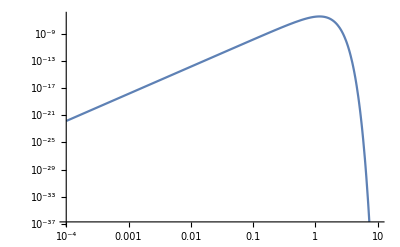

```mathematica
LogLogPlot[Evaluate[Exp[-Q^2 γ](Q^2(3 u)(1/(Exp[u/T]-1))+1/Δ Exp[-u/(Δ^2 γ)]Sum[1/(p!√(2 π p))y^p Exp[-x^2/(2p)],{p,2,400}])//.{y->2W Exp[-1/(2(Δ γ)^2)],x->u/Δ,T->0.01,W->Q^2 α0,ϵ->3/2 α2,γ->α0,Δ->√((4ϵ)/(3γ)-1/γ^2),α0->3/2,α2->3/8,u->.5}],{Q,.0001,10}]
```

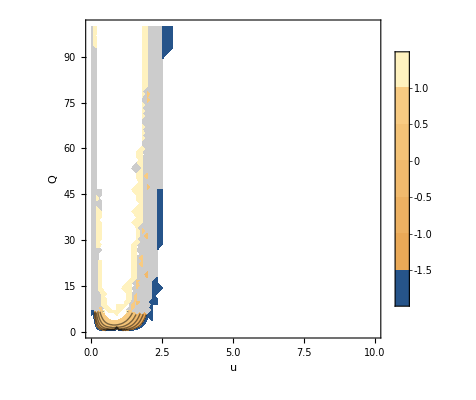

```mathematica
ContourPlot[Evaluate[Log[Exp[-Q^2 γ](Q^2(3 u)(1/(Exp[u/T]-1)+1)+1/Δ Exp[-u/(Δ^2 γ)]Sum[1/(p!√(2 π p))y^p Exp[-x^2/2 p],{p,2,400}])//.{y->2W Exp[-1/(2(Δ γ)^2)],x->u/Δ,T->0.01,W->Q^2 α0,ϵ->3/2 α2,γ->α0,Δ->√((4ϵ)/(3γ)-1/γ^2),α0->3/2,α2->3/8}]],{Q,0.01,10},{u,0,100},PlotRange->{-2,1},FrameLabel->{u,Q},PlotLegends->Automatic]
```

```mathematica
InelasticStructureFactor[Q_,u_,T_]=Evaluate[Exp[-Q^2 γ](Q^2(3 u)(1/(Exp[u/T]-1))HeavisideTheta[1-Abs[u]]+1/Δ Exp[-u/(Δ^2 γ)]Sum[1/(p!√(2 π p))y^p Exp[-x^2/(2p)],{p,2,400}])//.{y->2W Exp[-1/(2(Δ γ)^2)],x->u/Δ,W->Q^2 α0,ϵ->3/2 α2,γ->α0,Δ->√((4ϵ)/(3γ)-1/γ^2),α0->3/2,α2->3/8}];
InelasticStructureFactorMultiphononPiece[Q_,u_,T_]=Evaluate[Exp[-Q^2 γ](1/Δ Exp[-u/(Δ^2 γ)]Sum[1/(p!√(2 π p))y^p Exp[-x^2/(2p)],{p,2,20}])//.{y->2W Exp[-1/(2(Δ γ)^2)],x->u/Δ,W->Q^2 α0,ϵ->3/2 α2,γ->α0,Δ->√((4ϵ)/(3γ)-1/γ^2),α0->3/2,α2->3/8}];

SinglePhononApprox[Q_,u_,T_]:=Exp[-2 Q^2 α0] Q^2(3 u^2)/u(1/(ⅇ^(u/T)-1)+1)HeavisideTheta[1-Abs[u]]/.{α0->3/2};
ImpulseApprox[Q_,u_,T_]:=√(π/(Q^2 α2))Exp[(-(u-Q^2)^2)/(4 Q^2 α2)]HeavisideTheta[u-50]/.{α2->3/8};
```

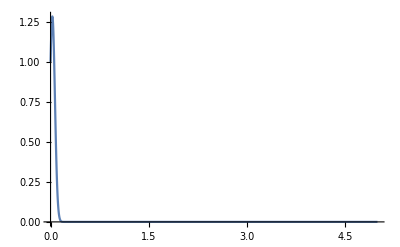

```mathematica
Plot[Exp[18u]Exp[-(18u)^2],{u,0,5},PlotRange->All]
```

```mathematica
Plot3D[{
(*InelasticStructureFactor[Q,-u,0.01],*)
SinglePhononApprox[Q,u,0.01],
ImpulseApprox[Q,u,0.01]}
,{Q,0.001,50},{u,0.001,200},AxesLabel->Automatic,PlotRange->All,PlotStyle->Opacity[0.7],PlotPoints->50]
```

-Graphics3D-

```mathematica
Table[InelasticStructureFactorMultiphononPiece[3.,u,0.01],{u,-10,0,1}]
```

{6107.46,2688.51,1017.2,324.192,84.8024,17.5824,2.75091,0.301567,0.0204668,0.000638795,2.30802×10^-7}

```mathematica
Plot3D[InelasticStructureFactorMultiphononPiece[Q,-u,0.01],{Q,0.001,10},{u,0.001,20},AxesLabel->Automatic,PlotRange->All,PlotStyle->Opacity[0.7]]
```

-Graphics3D-

```mathematica
Integrate[1/(√(2 π Γ))Exp[(-(ω-Er)^2)/(2 Γ)],{ω,-∞,∞},Assumptions->{Er >0,Γ>0}]
```

1

```mathematica
Integrate[(3 u^2)/u 1/(Exp[u/T]-1)Exp[-I u t],{u,-1,1},Assumptions->{T>0,t>0}]
```

3 (ⅇ^(-ⅈ t) T^2 HurwitzLerchPhi[ⅇ^(1/T),2,-ⅈ t T]-T^2 HurwitzZeta[2,-ⅈ t T]-(ⅈ ⅇ^(-ⅈ t) Hypergeometric2F1[1,-ⅈ t T,1-ⅈ t T,ⅇ^(1/T)])/t+1/(-ⅈ+t T)T (ⅇ^(ⅈ t+1/T) T (-ⅈ+t T) LerchPhi[ⅇ^(1/T),2,1+ⅈ t T]+ⅈ (ⅇ^(ⅈ t+1/T) Hypergeometric2F1[1,1+ⅈ t T,2+ⅈ t T,ⅇ^(1/T)]+T (1+ⅈ t T) Zeta[2,1+ⅈ t T,IncludeSingularTerm→False])))

```mathematica
%//FullSimplify
```

3 ⅇ^(-ⅈ t) T (-(ⅇ^(1/T))^(ⅈ t T) Beta[ⅇ^(1/T),-ⅈ t T,0]+ⅇ^(ⅈ t) π^2 T Csch[π t T]^2+T HurwitzLerchPhi[ⅇ^(1/T),2,-ⅈ t T]+ⅇ^(2 ⅈ t) (-(ⅇ^(1/T))^(-ⅈ t T) Beta[ⅇ^(1/T),1+ⅈ t T,0]+ⅇ^(1/T) T LerchPhi[ⅇ^(1/T),2,1+ⅈ t T]))

```mathematica
Integrate[Exp[-I u t]3 ⅇ^(-ⅈ t) T (-(ⅇ^(1/T))^(ⅈ t T) Beta[ⅇ^(1/T),-ⅈ t T,0]+ⅇ^(ⅈ t) π^2 T Csch[π t T]^2+T HurwitzLerchPhi[ⅇ^(1/T),2,-ⅈ t T]+ⅇ^(2 ⅈ t) (-(ⅇ^(1/T))^(-ⅈ t T) Beta[ⅇ^(1/T),1+ⅈ t T,0]+ⅇ^(1/T) T LerchPhi[ⅇ^(1/T),2,1+ⅈ t T]))/.T->.1,{t,-5,5},Assumptions->T>0]
```

$Aborted

```mathematica
1/(2π)Integrate[Exp[-I u t]Exp[I uu t]Exp[-ϵ t^2]f[uu],{t,-∞,∞},Assumptions->{ϵ>0}]
```

(ⅇ^(-(u-uu)^2/(4 ϵ)) f[uu])/(2 √π √ϵ)

```mathematica
Limit[(ⅇ^(-(u-uu)^2/(4 ϵ)) √π f[uu])/(√ϵ),ϵ->0,Assumptions->{u>0,uu>0}]
```

0

```mathematica
1/(2π)Integrate[(ⅇ^(-(u-uu)^2/(4 ϵ)) √π)/(√ϵ),{u,-∞,∞},Assumptions->{uu>0,ϵ>0}]
```

1

```mathematica
1/(2π)Integrate[Exp[-I u t]Exp[-ϵ t^2] Integrate[f[uu]Exp[-I uu t],{uu,-1,1}]^n,{t,-∞,∞},Assumptions->{ϵ>0}]
```

Integrate[ⅇ^(-ⅈ t u-t^2 ϵ) (∫_-1^1 ⅇ^(-ⅈ t uu) f[uu]ⅆuu)^n,{t,-∞,∞},Assumptions→{ϵ>0}]/(2 π)

```mathematica
Integrate[((3 (-u-u2)^2)/(-u-u2) 1/(Exp[(-u-u2)/T]-1))((3 u2^2)/u2 1/(Exp[u2/T]-1)),{u2,-1,1},Assumptions->{u>0&&u<1,T>0,t>0}]
```

-1/(-1+ⅇ^(u/T))3 ⅇ^(u/T) T (π^2 T u-6 u Log[-1+ⅇ^(1/T)]-3 Log[-1+ⅇ^((1-u)/T)]+3 u Log[-1+ⅇ^((1-u)/T)]+3 Log[-1+ⅇ^((1+u)/T)]+3 u Log[-1+ⅇ^((1+u)/T)]-6 T u PolyLog[2,ⅇ^(1/T)]+3 T (-2+u) PolyLog[2,ⅇ^((1-u)/T)]-3 T u PolyLog[2,ⅇ^(-u/T)]-3 T u PolyLog[2,ⅇ^(u/T)]+6 T PolyLog[2,ⅇ^((1+u)/T)]+3 T u PolyLog[2,ⅇ^((1+u)/T)]+6 T^2 PolyLog[3,ⅇ^((1-u)/T)]-6 T^2 PolyLog[3,ⅇ^(-u/T)]+6 T^2 PolyLog[3,ⅇ^(u/T)]-6 T^2 PolyLog[3,ⅇ^((1+u)/T)])

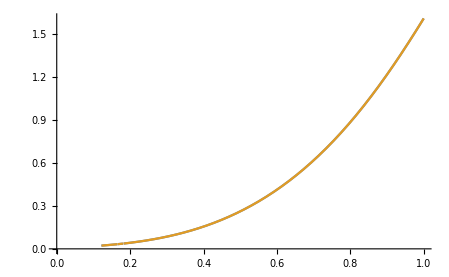

```mathematica
Plot[Evaluate[{-1/(-1+ⅇ^(u/T))3 ⅇ^(u/T) T (π^2 T u-6 u Log[-1+ⅇ^(1/T)]-3 Log[-1+ⅇ^((1-u)/T)]+3 u Log[-1+ⅇ^((1-u)/T)]+3 Log[-1+ⅇ^((1+u)/T)]+3 u Log[-1+ⅇ^((1+u)/T)]-6 T u PolyLog[2,ⅇ^(1/T)]+3 T (-2+u) PolyLog[2,ⅇ^((1-u)/T)]-3 T u PolyLog[2,ⅇ^(-u/T)]-3 T u PolyLog[2,ⅇ^(u/T)]+6 T PolyLog[2,ⅇ^((1+u)/T)]+3 T u PolyLog[2,ⅇ^((1+u)/T)]+6 T^2 PolyLog[3,ⅇ^((1-u)/T)]-6 T^2 PolyLog[3,ⅇ^(-u/T)]+6 T^2 PolyLog[3,ⅇ^(u/T)]-6 T^2 PolyLog[3,ⅇ^((1+u)/T)]),-1/(-1+ⅇ^(u/T))3 ⅇ^(u/T) T (3 ⅈ π-3 ⅈ π u+π^2 T u-6 u Log[-1+ⅇ^(1/T)]-3 Log[1-ⅇ^((1-u)/T)]+3 u Log[1-ⅇ^((1-u)/T)]+3 Log[-1+ⅇ^((1+u)/T)]+3 u Log[-1+ⅇ^((1+u)/T)]-6 T u PolyLog[2,ⅇ^(1/T)]+3 T (-2+u) PolyLog[2,ⅇ^((1-u)/T)]-3 T u PolyLog[2,ⅇ^(-u/T)]-3 T u PolyLog[2,ⅇ^(u/T)]+6 T PolyLog[2,ⅇ^((1+u)/T)]+3 T u PolyLog[2,ⅇ^((1+u)/T)]+6 T^2 PolyLog[3,ⅇ^((1-u)/T)]-6 T^2 PolyLog[3,ⅇ^(-u/T)]+6 T^2 PolyLog[3,ⅇ^(u/T)]-6 T^2 PolyLog[3,ⅇ^((1+u)/T)])}/.T->.05],{u,0,1}]
```

```mathematica
Integrate[((3 (-u-u2)^2)/(-u-u2) 1/(Exp[(-u-u2)/T]-1))((3 u2^2)/u2 1/(Exp[u2/T]-1)),{u2,-1,1},Assumptions->{u>1&&u<2,T>0,t>0}]
```

ConditionalExpression[-1/(-1+ⅇ^(u/T))3 ⅇ^(u/T) T (3 ⅈ π-3 ⅈ π u+π^2 T u-6 u Log[-1+ⅇ^(1/T)]-3 Log[1-ⅇ^((1-u)/T)]+3 u Log[1-ⅇ^((1-u)/T)]+3 Log[-1+ⅇ^((1+u)/T)]+3 u Log[-1+ⅇ^((1+u)/T)]-6 T u PolyLog[2,ⅇ^(1/T)]+3 T (-2+u) PolyLog[2,ⅇ^((1-u)/T)]-3 T u PolyLog[2,ⅇ^(-u/T)]-3 T u PolyLog[2,ⅇ^(u/T)]+6 T PolyLog[2,ⅇ^((1+u)/T)]+3 T u PolyLog[2,ⅇ^((1+u)/T)]+6 T^2 PolyLog[3,ⅇ^((1-u)/T)]-6 T^2 PolyLog[3,ⅇ^(-u/T)]+6 T^2 PolyLog[3,ⅇ^(u/T)]-6 T^2 PolyLog[3,ⅇ^((1+u)/T)]),ⅇ^(u/T)≥ⅇ^(1/T)]

```mathematica
TwoPhononFunctionPoints[T_]:=Table[{u,NIntegrate[((3 (-u-u2)^2)/(-u-u2) 1/(Exp[(-u-u2)/T]-1))((3 u2^2)/u2 1/(Exp[u2/T]-1))/.T->0.01,{u2,-1,1}]},{u,0,2,0.01}];
TwoPhononFunction[T_]:=Interpolation[TwoPhononFunctionPoints[T]]
```

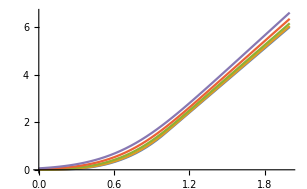

```mathematica
Plot[Evaluate[Table[TwoPhononFunction[T][u],{T,0.001,0.101,0.025}]],{u,0,2}]
```

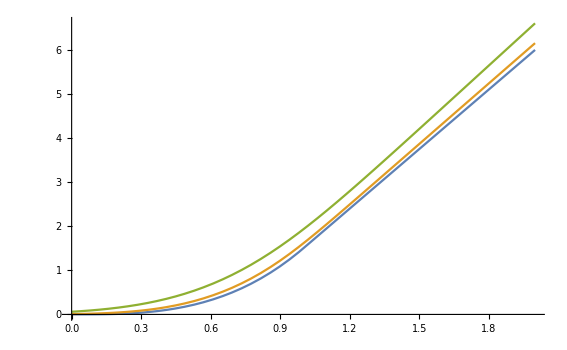

```mathematica
Plot[Evaluate[Table[TwoPhononFunction[T][u],{T,0.001,0.101,0.05}]],{u,0,2}]
```

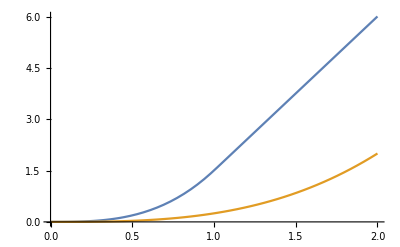

```mathematica
Plot[{Evaluate[TwoPhononFunction[T][u]/.T->0.00001],u^3/4},{u,0,2}]
```

```mathematica
Table[D[TwoPhononFunction[T][u]/.T->0.0001,{u,n}]/.u->0,{n,0,5}]
```

{0.0000592176,0.00298477,0.119854,5.97512,0.,0.}

```mathematica
6 π^2 T^3/.T->0.0001
```

5.92176×10^-11

```mathematica
Limit[D[-1/(-1+ⅇ^(u/T))3 ⅇ^(u/T) T (3 ⅈ π-3 ⅈ π u+π^2 T u-6 u Log[-1+ⅇ^(1/T)]-3 Log[1-ⅇ^((1-u)/T)]+3 u Log[1-ⅇ^((1-u)/T)]+3 Log[-1+ⅇ^((1+u)/T)]+3 u Log[-1+ⅇ^((1+u)/T)]-6 T u PolyLog[2,ⅇ^(1/T)]+3 T (-2+u) PolyLog[2,ⅇ^((1-u)/T)]-3 T u PolyLog[2,ⅇ^(-u/T)]-3 T u PolyLog[2,ⅇ^(u/T)]+6 T PolyLog[2,ⅇ^((1+u)/T)]+3 T u PolyLog[2,ⅇ^((1+u)/T)]+6 T^2 PolyLog[3,ⅇ^((1-u)/T)]-6 T^2 PolyLog[3,ⅇ^(-u/T)]+6 T^2 PolyLog[3,ⅇ^(u/T)]-6 T^2 PolyLog[3,ⅇ^((1+u)/T)]),{u,4}],u->0,Assumptions->T>0]//FullSimplify
```

1/(5 T^3)(3-432/((-1+ⅇ^(1/T))^5)-6 ⅈ π T+15 T^2+π^2 T^2+(108 (-10+3 T))/((-1+ⅇ^(1/T))^4)+(-45+84 T (1+T))/(-1+ⅇ^(1/T))+(12 (-80+9 T (6+T)))/((-1+ⅇ^(1/T))^3)+(6 (-60+T (68+27 T)))/((-1+ⅇ^(1/T))^2)-6 T Log[-1+ⅇ^(1/T)]-6 T^2 PolyLog[2,ⅇ^(1/T)])

```mathematica
Limit[%,T->0]
```

∞

```mathematica
Limit[D[6 T (-3-3/(-1+ⅇ^(1/T))+π T (6 ⅈ-π T)+6 T Log[-1+ⅇ^(1/T)]+6 T^2 PolyLog[2,ⅇ^(1/T)]),{T,4}],T->0]
```

0

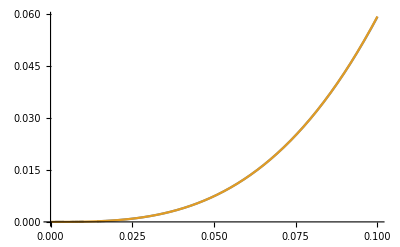

```mathematica
Plot[{6 T (-3-3/(-1+ⅇ^(1/T))+π T (6 ⅈ-π T)+6 T Log[-1+ⅇ^(1/T)]+6 T^2 PolyLog[2,ⅇ^(1/T)]),
6 π^2 T^3},{T,0,0.1}]
```

```mathematica
Integrate[Exp[-I u t]t,{t,-∞,∞}]
```

Integrate::idiv: Integral of ⅇ^(-ⅈ t u) t does not converge on {-∞,∞}.

∫_(-∞)^∞ ⅇ^(-ⅈ t u) tⅆt

```mathematica
Series[1/(√(4 π ωl^2 Q^2 α2))Exp[(-(u-Q^2)^2)/(4 Q^2 α2)]]
```

ⅇ^(-((-Q^2+u)^2)/(4 Q^2 α2)) ((√(α2 ωl^2))/(2 √π α2 ωl^2 Q)+O[Q]^5)

```mathematica
Exp[(-Expand[(u-Q^2)^2])/(4 Q^2 α2)]
```

ⅇ^(-(Q^4-2 Q^2 u+u^2)/(4 Q^2 α2))

```mathematica
1/(2ωl Q √(π α2))ⅇ^(-Q^2/(4 α2))ⅇ^(u/(2 α2))ⅇ^(-u^2/(4 Q^2 α2))
```

```mathematica
Limit[1/(2ωl Q √(π α2))ⅇ^(-Q^2/(4 α2))ⅇ^(u/(2 α2))ⅇ^(-u^2/(4 Q^2 α2)),Q->0,Assumptions->{ωl>0,α2>0,u>0}]
```

0

```mathematica
Integrate[Z[u]/u Coth[u/(2T)],{u,0,1}]
```

```mathematica
Integrate[Z[u]/u(n[u]-n[-u]),{u,0,1}]
```

```mathematica
Integrate[Z[u]/u n[u],{u,0,1}]+Integrate[Z[u]/u n[u],{u,-1,0}]
```

```mathematica
-Integrate[Exp[-I uu t]3uu,{uu,-1,0}]//FullSimplify
```

(-3+ⅇ^(ⅈ t) (3-3 ⅈ t))/t^2

```mathematica
Integrate[Exp[-I u t]((-3+ⅇ^(ⅈ t) (3-3 ⅈ t))/t^2),{t,-∞,∞},Assumptions->u>0]
```

3 π (u-Abs[-1+u]+Sign[1-u])

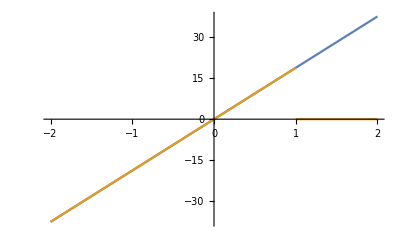

```mathematica
Plot[{6π u,3 π (u-Abs[-1+u]+Sign[1-u])},{u,-2,2}]
```

```mathematica
Integrate[Exp[-I u t]((-3+ⅇ^(ⅈ t) (3-3 ⅈ t))/t^2)^2,{t,-∞,∞},Assumptions->u>0]
```

3/2 (-4 ⅈ-6 π+ⅈ u+3 π u+π u^3-4 ⅈ Log[1-u]+6 ⅈ u Log[1-u]-2 ⅈ u^3 Log[1-u]+16 ⅈ Log[2-u]-12 ⅈ u Log[2-u]+ⅈ u^3 Log[2-u]-12 ⅈ Log[-ⅈ (-2+u)]+6 ⅈ u Log[-ⅈ (-2+u)]+ⅈ u^3 Log[u]+6 π (-1+u^2) Sinh[2 ArcCoth[u]]+2 π (-1+u^2)^(3/2) Sinh[3 ArcCoth[u]]+24 π Sinh[2 ArcTanh[2/u]]-6 π u^2 Sinh[2 ArcTanh[2/u]]+4 π √(-4+u^2) Sinh[3 ArcTanh[2/u]]-π u^2 √(-4+u^2) Sinh[3 ArcTanh[2/u]])+1/4 (-30 ⅈ (-2+u)-11 ⅈ u^3+6 ⅈ EulerGamma u^3-3 π u^3+12 ⅈ (-1+u^2) Cosh[2 ArcTanh[1/u]]+36 π (-1+u^2) Cosh[2 ArcTanh[1/u]]+12 π (1-1/u^2)^(3/2) u^3 Cosh[3 ArcTanh[1/u]]-12 ⅈ (-4+u^2) Cosh[2 ArcTanh[2/u]]-36 π (-4+u^2) Cosh[2 ArcTanh[2/u]]-6 π (1-4/u^2)^(3/2) u^3 Cosh[3 ArcTanh[2/u]]-6 ⅈ (-2+u) (-11+6 EulerGamma+6 Log[ⅈ (-2+u)])+6 ⅈ u^3 Log[u]-2 ⅈ u^3 (-11+6 EulerGamma-3 ⅈ π+6 Log[u])-12 ⅈ (-1+u^2) Sinh[2 ArcTanh[1/u]]-36 π (-1+u^2) Sinh[2 ArcTanh[1/u]]+6 ⅈ (-1+u^2) (Cosh[2 ArcTanh[1/u]] (-11+6 EulerGamma-3 ⅈ π+3 Log[1-1/u^2]+6 Log[u])+6 ArcTanh[1/u] Sinh[2 ArcTanh[1/u]])+216 ⅈ (-1+u^2) (-1/6 ArcTanh[1/u] Cosh[2 ArcTanh[1/u]]-1/36 (-11+6 EulerGamma-3 ⅈ π+3 Log[1-1/u^2]+6 Log[u]) Sinh[2 ArcTanh[1/u]])-12 π (1-1/u^2)^(3/2) u^3 Sinh[3 ArcTanh[1/u]]+2 ⅈ √(1-1/u^2) u (-1+u^2) (Cosh[3 ArcTanh[1/u]] (-11+6 EulerGamma-3 ⅈ π+3 Log[1-1/u^2]+6 Log[u])+6 ArcTanh[1/u] Sinh[3 ArcTanh[1/u]])-2 ⅈ √(1-1/u^2) u (-1+u^2) (6 ArcTanh[1/u] Cosh[3 ArcTanh[1/u]]+(-11+6 EulerGamma-3 ⅈ π+3 Log[1-1/u^2]+6 Log[u]) Sinh[3 ArcTanh[1/u]])+12 ⅈ (-4+u^2) Sinh[2 ArcTanh[2/u]]+36 π (-4+u^2) Sinh[2 ArcTanh[2/u]]-6 ⅈ (-4+u^2) (Cosh[2 ArcTanh[2/u]] (-11+6 EulerGamma-3 ⅈ π+3 Log[1-4/u^2]+6 Log[u])+6 ArcTanh[2/u] Sinh[2 ArcTanh[2/u]])-216 ⅈ (-4+u^2) (-1/6 ArcTanh[2/u] Cosh[2 ArcTanh[2/u]]-1/36 (-11+6 EulerGamma-3 ⅈ π+3 Log[1-4/u^2]+6 Log[u]) Sinh[2 ArcTanh[2/u]])+6 π (1-4/u^2)^(3/2) u^3 Sinh[3 ArcTanh[2/u]]-ⅈ √(1-4/u^2) u (-4+u^2) (Cosh[3 ArcTanh[2/u]] (-11+6 EulerGamma-3 ⅈ π+3 Log[1-4/u^2]+6 Log[u])+6 ArcTanh[2/u] Sinh[3 ArcTanh[2/u]])+ⅈ √(1-4/u^2) u (-4+u^2) (6 ArcTanh[2/u] Cosh[3 ArcTanh[2/u]]+(-11+6 EulerGamma-3 ⅈ π+3 Log[1-4/u^2]+6 Log[u]) Sinh[3 ArcTanh[2/u]]))

```mathematica
(1/(Exp[u/T]-1))/(Exp[-u/(2T)]/(2Sinh[u/(2T)]))//FullSimplify
```

1

```mathematica
Sinh[x]
```

Sinh[x]

```mathematica
(Exp[u/(2T)]-Exp[-u/(2T)])/2//FullSimplify
```

Sinh[u/(2 T)]

```mathematica
m0/(2 M β)3 u^2
```

```mathematica
Integrate[1/(R √(2 π))Exp[-ξ^2/(2 R^2)],{ξ,-θ,θ},Assumptions->{R>0,θ>0}]
```

Erf[θ/(√2 R)]

```mathematica
Integrate[1/(R √(2 π))Exp[-ξ^2/(2 R^2)],{ξ,0,∞},Assumptions->{R>0,θ>0}]
```

1/2

```mathematica
Integrate[(3 u^2)/(u Sinh[u/(2 T)]),{u,0,1},Assumptions->{T>0,θ>0}]
```

3 T (π^2 T+2 Log[Tanh[1/(4 T)]]+2 T PolyLog[2,ⅇ^(-1/T)]-8 T PolyLog[2,ⅇ^(-1/2/T)])

```mathematica
Table[Limit[D[3 T (π^2 T+2 Log[Tanh[1/(4 T)]]+2 T PolyLog[2,ⅇ^(-1/T)]-8 T PolyLog[2,ⅇ^(-1/2/T)]),{T,n}],T->0],{n,0,4}]
```

{0,0,6 π^2,0,0}

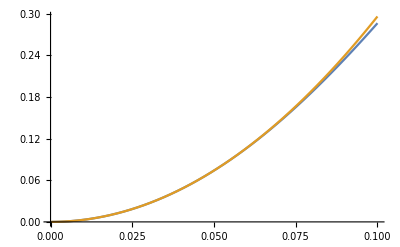

```mathematica
Plot[{3 T (π^2 T+2 Log[Tanh[1/(4 T)]]+2 T PolyLog[2,ⅇ^(-1/T)]-8 T PolyLog[2,ⅇ^(-1/2/T)]),3 π^2 T^2},{T,0,.1}]
```

```mathematica
Integrate[m/(2 M β)(3 ξ^2)/(ξ Sinh[ξ/(2 T)]),{ξ,-∞,∞},Assumptions->{T>0,θ>0}]
```

(3 m π^2 T^2)/(M β)

```mathematica
Integrate[m/(2 M β)(3 ξ^2)/(ξ Sinh[ξ/(2 T)]),{ξ,-∞,∞},Assumptions->{T>0,θ>0}]
```

```mathematica
Limit[m/(2 M β)(3 ξ^2)/(ξ Sinh[ξ/(2 T)]),ξ->0]
```

(3 m T)/(M β)

```mathematica
Limit[1/(2β)(3 u^2)/(u Sinh[u/(2T)]),u->0]
```

(3 T)/β

```mathematica
1/(R √(2π))Exp[-u^2/(2 R^2)]/.u->0
```

1/(√(2 π) R)

```mathematica
Solve[1/(√(2 π) R)==(3 T)/β,R]
```

{{R→β/(3 √(2 π) T)}}

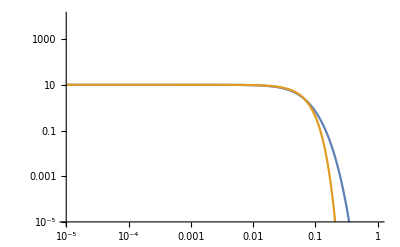

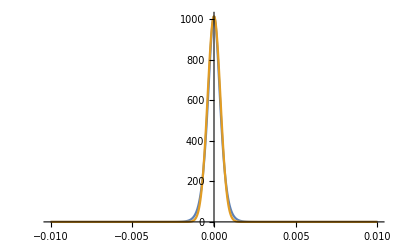

```mathematica
LogLogPlot[Evaluate[{1/(2β)(3 u^2)/(u Sinh[u/(2T)]),1/(R √(2π))Exp[-u^2/(2 R^2)]}//.{R->β/(3 √(2 π) T),β->3 π^2 T^2}/.T->.01],{u,10^-5,1},PlotRange->{10^-5,10^4}]
Plot[Evaluate[{1/(2β)(3 u^2)/(u Sinh[u/(2T)]),1/(R √(2π))Exp[-u^2/(2 R^2)]}//.{R->β/(3 √(2 π) T),β->3 π^2 T^2}/.T->.0001],{u,-.01,.01},PlotRange->All]
```

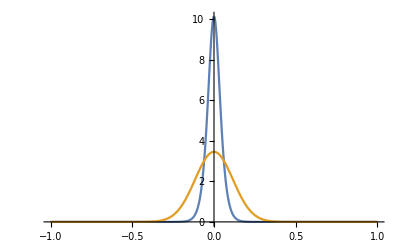

```mathematica
Plot[Evaluate[{1/(2β)(3 u^2)/(u Sinh[u/(2T)]),1/(R √(2π))Exp[-u^2/(2 R^2)]}//.{R->√((2T)/α),α->3/2,β->3 π^2 T^2}/.T->.01],{u,-1,1},PlotRange->All]
```

```mathematica
Integrate[(3 u^2)/u Coth[u/(2 T)],{u,0,1},Assumptions->{T>0,θ>0}]//FullSimplify
Integrate[(3 u^2)/(u Sinh[u/(2 T)]),{u,0,1},Assumptions->{T>0,θ>0}]//FullSimplify
```

3/2+π^2 T^2+6 T Log[1-ⅇ^(-1/T)]-6 T^2 PolyLog[2,ⅇ^(-1/T)]

3 T (π^2 T+2 Log[Tanh[1/(4 T)]]+2 T PolyLog[2,ⅇ^(-1/T)]-8 T PolyLog[2,ⅇ^(-1/2/T)])

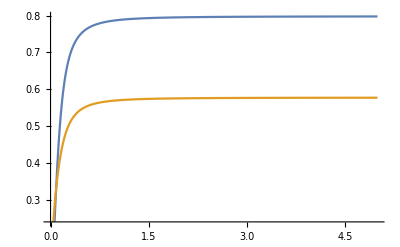

```mathematica
Plot[Evaluate[{β/(3 √(2 π) T),√((2T)/α)}/.{α->3/2+π^2 T^2+6 T Log[1-ⅇ^(-1/T)]-6 T^2 PolyLog[2,ⅇ^(-1/T)],β->3 T (π^2 T+2 Log[Tanh[1/(4 T)]]+2 T PolyLog[2,ⅇ^(-1/T)]-8 T PolyLog[2,ⅇ^(-1/2/T)])}],{T,0,5}]
```

```mathematica
Integrate[(1/(R √(2π))Exp[-u1^2/(2 R^2)])(1/(R √(2π))Exp[-u2^2/(2 R^2)])/.{u1->-u-u2},{u2,-∞,∞},Assumptions->{u>0,R>0}]
```

(ⅇ^(-u^2/(4 R^2)))/(2 √π R)

```mathematica
Integrate[(1/(R √(2π))Exp[-u1^2/(2 R^2)])(1/(R √(2π))Exp[-u2^2/(2 R^2)])(1/(R √(2π))Exp[-u3^2/(2 R^2)])/.{u1->-u-u2-u3},{u2,-∞,∞},{u3,-∞,∞},Assumptions->{u>0,R>0}]
```

(ⅇ^(-u^2/(6 R^2)))/(√(6 π) R)

```mathematica
Integrate[(1/(R √(2π))Exp[-u1^2/(2 R^2)])(1/(R √(2π))Exp[-u2^2/(2 R^2)])(1/(R √(2π))Exp[-u3^2/(2 R^2)])(1/(R √(2π))Exp[-u4^2/(2 R^2)])/.{u1->-u-u2-u3-u4},{u2,-∞,∞},{u3,-∞,∞},{u4,-∞,∞},Assumptions->{u>0,R>0}]
```

(ⅇ^(-u^2/(8 R^2)))/(2 √(2 π) R)

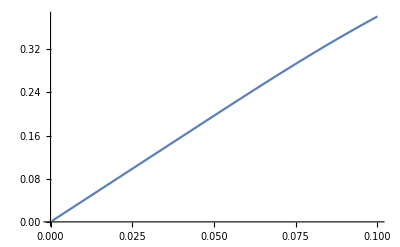

```mathematica
Plot[Evaluate[β/(3 √(2 π) T)/.{β->3 T (π^2 T+2 Log[Tanh[1/(4 T)]]+2 T PolyLog[2,ⅇ^(-1/T)]-8 T PolyLog[2,ⅇ^(-1/2/T)])}],{T,0,.1}]
```

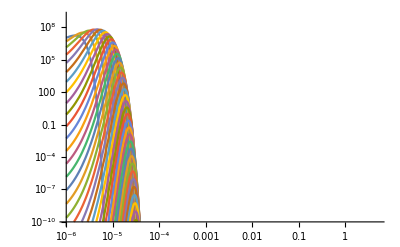

```mathematica
LogLogPlot[Evaluate[Table[1/(n!√(2π n R^2))Exp[u/(2T)]Exp[-u^2/(2n R^2)]//.{R->β/(3 √(2 π) T),β->3 π^2 T^2,T->0.0000001},{n,2,100}]],{u,0.000001,5},PlotRange->{10^-10,1000000000}]
```

```mathematica
1/(Exp[u/T]-1)-(Exp[-u/(2T)]/(2Sinh[u/(2T)]))//FullSimplify
```

0

```mathematica
Integrate[1/(2β)(3 u^2)/(u Sinh[u/(2T)]),{u,-1,1},Assumptions->T>0]/.β->Integrate[(3 u^2)/(u Sinh[u/(2 T)]),{u,0,1},Assumptions->{T>0}]
```

1

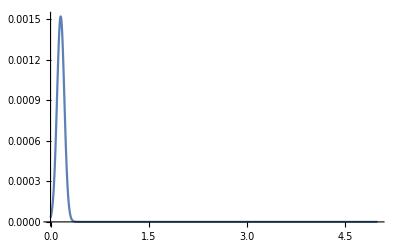

```mathematica
Plot[Evaluate[Sum[β^n/(n!√(2π n R^2))Exp[u/(2T)]Exp[-u^2/(2n R^2)]//.{R->β/(3 √(2 π) T),β->3 π^2 T^2,T->0.01},{n,2,5000}]],{u,0.000001,5},PlotRange->All]
```

```mathematica
1/(Exp[u/T]-1)+1//FullSimplify
```

1+1/(-1+ⅇ^(u/T))

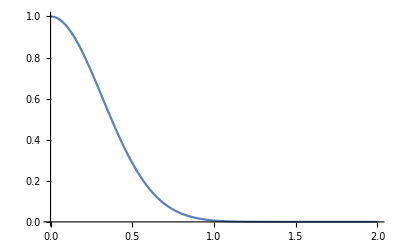

```mathematica
Plot[Exp[-u^2/(.2)],{u,0,2},PlotRange->{0,1}]
```

```mathematica
Integrate[(3 u^2)/(u Sinh[u/(2T)]),{u,0,1},Assumptions->T>0]
```

3 T (π^2 T+2 Log[Tanh[1/(4 T)]]+2 T PolyLog[2,ⅇ^(-1/T)]-8 T PolyLog[2,ⅇ^(-1/2/T)])

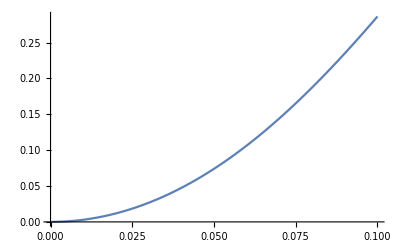

```mathematica
Plot[3 T (π^2 T+2 Log[Tanh[1/(4 T)]]+2 T PolyLog[2,ⅇ^(-1/T)]-8 T PolyLog[2,ⅇ^(-1/2/T)]),{T,0,.1}]
```

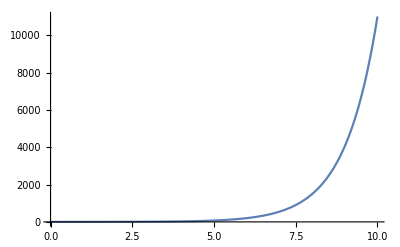

```mathematica
Plot[Sinh[x],{x,0,10},PlotRange->All]
```

```mathematica
3/(4(2*3/8))
```

1

```mathematica
(4(1))/(3(3/2))-(3/2)^-2
```

4/9

```mathematica
3/4(2*3/8)
```

9/16

```mathematica
(4(9/16))/(3(3/2))-(3/2)^-2
```

1/18

```mathematica
Integrate[3 u^3 Coth[u/(2T)],{u,0 ,1},Assumptions->T>0]
```

-3/4+6 ⅈ π T-(2 π^4 T^4)/5+6 T Log[-1+ⅇ^(1/T)]+18 T^2 PolyLog[2,ⅇ^(1/T)]-36 T^3 PolyLog[3,ⅇ^(1/T)]+36 T^4 PolyLog[4,ⅇ^(1/T)]

```mathematica
Limit[%,T->0]
```

3/4

```mathematica
Integrate[(1/(R √(2π))Exp[-u1^2/(2 R^2)])(1/(R √(2π))Exp[-u2^2/(2 R^2)])/.{u1->-u-u2},{u2,0,∞},Assumptions->{u>0,R>0}]
```

(ⅇ^(-u^2/(4 R^2)) (1+Erf[u/(2 R)]))/(4 √π R)

```mathematica
Integrate[(1/(R √(2π))Exp[-u1^2/(2 R^2)])(1/(R √(2π))Exp[-u2^2/(2 R^2)])(1/(R √(2π))Exp[-u3^2/(2 R^2)])/.{u1->u-u2-u3},{u2,0,∞},{u3,0,∞},Assumptions->{u>0,R>0}]
```

Integrate[(ⅇ^(-(u^2-2 u u2+3 u2^2)/(4 R^2)) (1+Erf[(u-u2)/(2 R)]))/(4 √2 π R^2),{u2,0,∞},Assumptions→{u>0,R>0}]

```mathematica
Integrate[(1/(R √(2π))Exp[-u1^2/(2 R^2)])(1/(R √(2π))Exp[-u2^2/(2 R^2)])(1/(R √(2π))Exp[-u3^2/(2 R^2)])(1/(R √(2π))Exp[-u4^2/(2 R^2)])/.{u1->u-u2-u3-u4},{u2,-∞,∞},{u3,-∞,∞},{u4,-∞,∞},Assumptions->{u>0,R>0}]
```

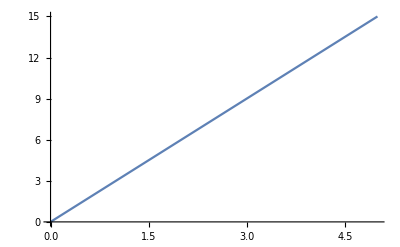

```mathematica
Plot[(3 u^2)/u/.T->.1,{u,0,5}]
```

```mathematica
Integrate[((3u1)/Exp[u1/(2T)])((3u2)/Exp[u2/(2T)])((3u3)/Exp[u3/(2T)])((3u4)/Exp[u4/(2T)])/.u1->-u-u2-u3-u4,{u2,-1,1},{u3,-1,1},{u4,-1,1}]
```

0

```mathematica
1-(q^2 Sin[θq]^2)/(k^2+q^2-2 k q Cos[θq])//FullSimplify
```

(k-q Cos[θq])^2/(k^2+q^2-2 k q Cos[θq])

```mathematica
(k-q cθ)/(√(k^2+q^2-2 k q cθ))/.{q->k cθ+√(ω(ω-2 k)+k^2 cθ^2)}//FullSimplify
```

(k-cθ^2 k-cθ √(cθ^2 k^2+ω (-2 k+ω)))/(√((k-ω)^2))

```mathematica
(k-cθ^2 k-cθ √(cθ^2 k^2+ω (-2 k+ω)))/(k-ω)//Expand//FullSimplify
```

(k-cθ^2 k-cθ √(cθ^2 k^2-2 k ω+ω^2))/(k-ω)

```mathematica
D[(k-cθ^2 k-cθ √(cθ^2 k^2+ω (-2 k+ω)))/(k-ω),cθ]//FullSimplify
```

-((cθ k+√(cθ^2 k^2+ω (-2 k+ω)))^2)/((k-ω) √(cθ^2 k^2+ω (-2 k+ω)))

```mathematica
-((cθ k+√(cθ^2 k^2+ω (-2 k+ω)))^2)/((k-ω) √(cθ^2 k^2+ω (-2 k+ω)))//Expand//FullSimplify
```

(-2 cθ^2 k^2+(2 k-ω) ω-2 cθ k √(cθ^2 k^2+ω (-2 k+ω)))/((k-ω) √(cθ^2 k^2+ω (-2 k+ω)))

```mathematica
Series[((cθ k+√(cθ^2 k^2+ω (-2 k+ω)))^2)/((k-ω) √(cθ^2 k^2+ω (-2 k+ω))),{ω,0,2}]//FullSimplify[#,Assumptions->{cθ<0,k>0}]&
```

-ω^2/(cθ^3 k^2)+O[ω]^3

```mathematica
k^2+(k-ω)^2-2 k(k-ω)cθ/.cθ->1//FullSimplify
k^2+(k-ω)^2-2 k(k-ω)cθ/.cθ->-1//FullSimplify
```

ω^2

(-2 k+ω)^2

```mathematica
Series[√(k^2+(k-ω)^2-2 k(k-ω)cθ1),{ω,0,2}]//FullSimplify
```

√(2 k^2-2 cθ1 k^2)-(√(-(-1+cθ1) k^2) ω)/(√2 k)+((1+cθ1) ω^2)/(4 √2 √(-(-1+cθ1) k^2))+O[ω]^3

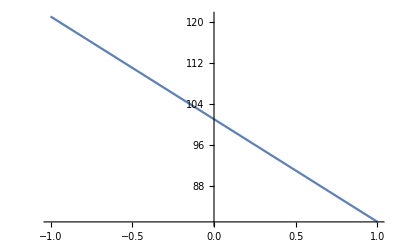

```mathematica
Plot[k^2+(k-ω)^2-2 k(k-ω)cθ/.{k->10,ω->9},{cθ,-1,1}]
```

```mathematica
2 π Integrate[m/(-k(k-ω))(mi/(2 π))^2((4 π Z α)/(2 m Er+λ^2))^2 Exp[(-(ω-Er)^2)/(4 ωD Er α2)]/(√(4 π ωD Er α2)),{Er,(2 k-ω)^2/(2 m),ω^2/(2 m)},Assumptions->{ω>0,m>0,k>0,ωD>0,α2>0,λ>0,ω<k}]
```

2 π Integrate[-(2 ⅇ^(-(-Er+ω)^2/(4 Er α2 ωD)) m mi^2 Z^2 α^2)/(k √π (2 Er m+λ^2)^2 (k-ω) √(Er α2 ωD)),{Er,(2 k-ω)^2/(2 m),ω^2/(2 m)},Assumptions→{ω>0,m>0,k>0,ωD>0,α2>0,λ>0,ω<k}]

```mathematica
% //FullSimplify
```

$Aborted

```mathematica
Integrate[1/(x+1)^2 Exp[(-(x-1)^2)/x]/(√x),{x,1,2}]
```

∫_1^2 (ⅇ^(-(-1+x)^2/x))/(√x (1+x)^2)ⅆx

```mathematica
2 π m/(-k(k-ω))(mi/(2 π))^2((4 π Z α)/(2 m ωD))^2 //FullSimplify
```

-(2 mi^2 π Z^2 α^2)/(k m (k-ω) ωD^2)

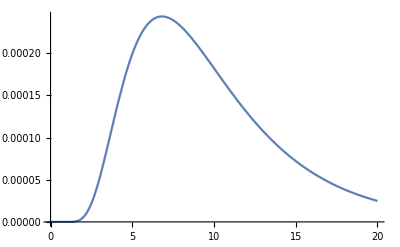

```mathematica
Plot[Exp[(-(u-Q2)^2)/(4Q2 α2)]/((Q2+η2)^2 √(4π Q2 α2))/.{α2->3/2,u->10,η2->10},{Q2,0,20},PlotRange->All]
```

```mathematica
√(2Q2 α2)//.{Q2->u,u->100,α2->3/2.}
```

17.3205

```mathematica
((4 α Ef √(Ef^2+m^2))/π)/(2M ωD)//.{α->1/137,Ef->(3 π^2 ne)^(1/3),ne->Z ni,ni->1,Z->6,m->0.5,M->10^4,ωD->cs(6 π^2 ni)^(1/3),cs->10^-2}
```

0.000378241

```mathematica
Clear[dσdω];
dσdω[κ_]:=dσdω[κ]=Evaluate[Interpolation[Table[{u,Quiet@NIntegrate[Exp[(-(u-Q2)^2)/(4Q2 α2)]/((Q2+η2)^2 √(4π Q2 α2))/.{α2->3/2,η2->10^-4},{Q2,10^-6 u^2,10^-6(2 κ-u)^2}]},{u,10,10^3,1}]]];
```

```mathematica
dσdω[10^5][u]
```

InterpolatingFunction[{{10., 1000.}}, <>][u]

```mathematica
dσdω[10^5][u]
```

InterpolatingFunction[{{1., 1000.}}, <>][u]

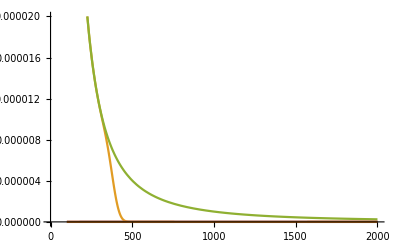

```mathematica
Plot[Evaluate[Table[dσdω[10^n][u],{n,3,8}]],{u,100,2000},PlotRange->{0,0.00002}]
```

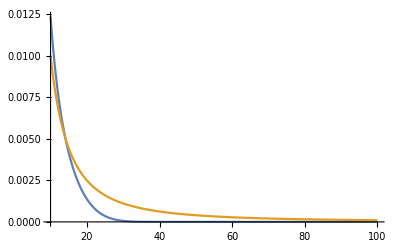
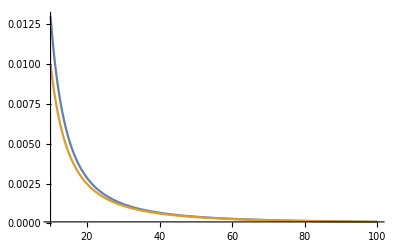
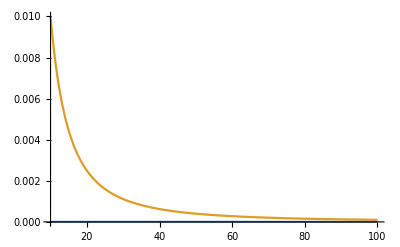
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Plot[{dσdω[2*10^n][u],1/(u+η2)^2/.{η2->10^-4}},{u,10,100},PlotRange->All],{n,3,8}]
```

```mathematica
cs(6 π^2 ni)^(1/3)/.{ni->1,cs->0.01}
```

0.0389778

```mathematica
(Z^2 α)/((4π)/3 ni)^(-1/3)/.{Z->6,α->1/137.,ni->1}
```

0.423589

```mathematica
((Z^2 α)/((4π)/3 ni)^(-1/3))/T/.{Z->6,α->1/137.,ni->1,T->0.002}
```

211.795

```mathematica
.5*((4π Z^2 α ni)/M)^(1/2)/.{Z->6,α->1/137.,ni->1,T->0.002,M->10^4}
```

0.00908586

```mathematica
1/β^2(1-β^2 ω/Ekin)//.{Ekin->(2 M β^2 γ^2)/(1+2 γ M/m+(M/m)),γ->k/m}//FullSimplify
```

(2-((2 k M+m (m+M)) ω)/(k^2 M))/(2 β^2)

m^2/(k (k-ω))

```mathematica
Coth[∞]
```

1

```mathematica
Sum[x^n/(n!)(n ω),{n,0,∞}]
```

ⅇ^x x ω

```mathematica
ω0/(2M)(κ^2+(κ-u)^2-2κ(κ-u)cθ)/.cθ->-1//FullSimplify
ω0/(2M)(κ^2+(κ-u)^2-2κ(κ-u)cθ)/.cθ->1//FullSimplify
```

((u-2 κ)^2 ω0)/(2 M)

(u^2 ω0)/(2 M)

```mathematica
(2 π M)/(ω0 κ^2)(m/(2 π))^2((4 π Z α)/(2 M ω0))^2//FullSimplify
```

(2 m^2 π Z^2 α^2)/(M κ^2 ω0^3)

```mathematica
Integrate[(Q2^n Exp[-Q2])/(Q2+η2)^2,{Q2,Q21,Q22},Assumptions->{η2>0,Q21>0,Q22>Q21,n>0}]
```

Integrate[(ⅇ^-Q2 Q2^n)/(Q2+η2)^2,{Q2,Q21,Q22},Assumptions→{η2>0,Q21>0,Q22>Q21,n>0}]

```mathematica
Integrate[1/(√(4π T Er))Exp[(-(ω-Er)^2)/(4T Er)],{Er,0,∞},Assumptions->{T>0,ω>0}]
```

1

```mathematica
Integrate[1/(√(4π T Er))Exp[(-(ω-Er)^2)/(4T Er)],{Er,0,∞},Assumptions->{T>0,ω>0}]
```

```mathematica
Manipulate[Plot[1/(√(4π T Er))Exp[(-(ω-Er)^2)/(4T Er)]/.{ω->10},{Er,0,20},PlotRange->All],{T,0.0001,1}]
```

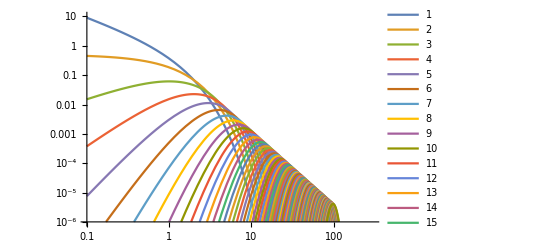

```mathematica
LogLogPlot[Evaluate[Table[Exp[-x]/x^2 x^n/(n!),{n,1,100}]],{x,0.1,300},PlotRange->{10^-6,10},PlotLegends->Automatic]
```

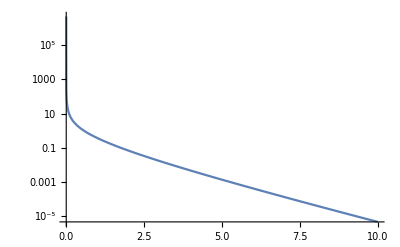
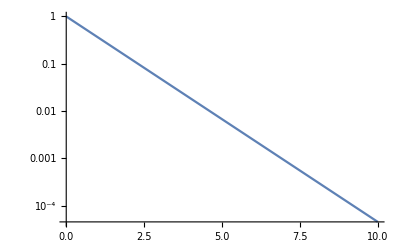
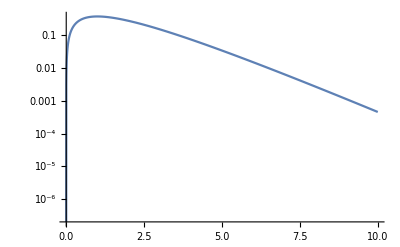
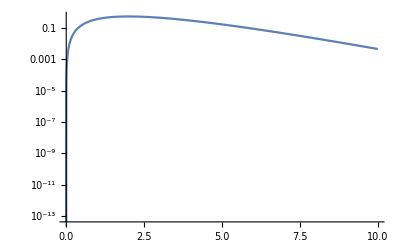
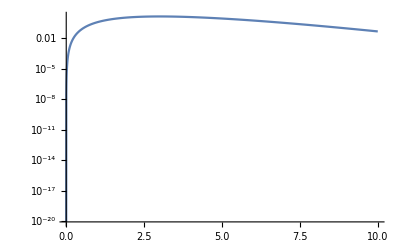

```mathematica
Table[LogPlot[Exp[-x]/x^2 x^n,{x,0,10},PlotRange->All],{n,1,5}]
```

```mathematica
Integrate[1/(n!)(Q2^n Exp[-Q2])/η2^2,{Q2,Q21,Q22},Assumptions->{Q21>0,Q22>Q21,n>1,n∈Integers}]
```

(Gamma[1+n,Q21]-Gamma[1+n,Q22])/(η2^2 n!)

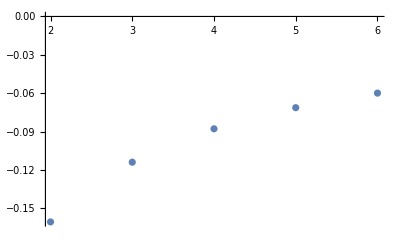

```mathematica
ListPlot[Table[{n,Gamma[n+1,1]-n!},{n,2,6}]]
```

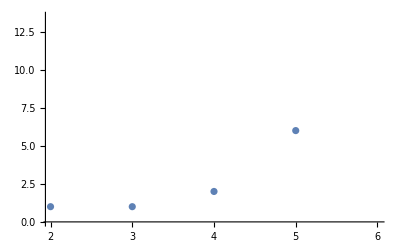

```mathematica
ListPlot[Table[{n,Gamma[n-1]},{n,2,6}]]
```

```mathematica
Integrate[1/(n!)(Q2^n Exp[-Q2])/(Q2+0)^2,{Q2,Q21,Q22},Assumptions->{Q21>0,Q22>Q21,n>1,n∈Integers}]
```

(Gamma[-1+n,Q21]-Gamma[-1+n,Q22])/(n!)

```mathematica
NIntegrate[(Q2^n Exp[-Q2])/(Q2+0)^2/.n->1,{Q2,.0000000000000001,3000}]
```

36.2641

```mathematica
NIntegrate[(Q2^n Exp[-Q2])/(Q2+0)^2/.n->2,{Q2,0,3000}]
```

1.

```mathematica
NIntegrate[(Q2^n Exp[-Q2])/(Q2+0)^2/.n->3,{Q2,0,3000}]
```

1.

```mathematica
NIntegrate[(Q2^n Exp[-Q2])/(Q2+0)^2/.n->8,{Q2,0,4000}]
```

720.

```mathematica
2π Integrate[M/k^2(m/(2π))^2((4π Z α)/(2M Er+λ^2))^2(6/((2π)^3 ni)((2m Er)ω)/(2M cs^3)),{Er,0,2 k^2/M},Assumptions->{k>0,M>0,λ>0,m>0}]
```

(3 m^3 Z^2 α^2 ω (-(4 k^2)/(4 k^2+λ^2)-2 Log[λ]+Log[4 k^2+λ^2]))/(2 cs^3 k^2 M^2 ni π^2)

```mathematica
2π M/k^2(m/(2π))^2((4π Z α)/(2M ω))^2
```

(2 m^2 π Z^2 α^2)/(k^2 M ω^2)

```mathematica
Integrate[DiracDelta[ω-Er],{Er,ω^2/(2M),(2k-ω)^2/(2M)},Assumptions->{ω>0,M>0,k>ω}]
```

HeavisideTheta[ω-ω^2/(2 M),(-2 M ω+(-2 k+ω)^2)/M]

```mathematica
2π Integrate[(k-ω)/k(m/(2π))^2((4π Z α)/q2)^2 DiracDelta[ω-q2/(2M)]/.{q2->k^2+(k-ω)^2-2k(k-ω)cθ},{cθ,-1,1},Assumptions->{ω>0,k>ω}]
```

ConditionalExpression[(2 m^2 π Z^2 α^2 Abs[M] Boole[-1<(2 k^2-2 (k+M) ω+ω^2)/(2 k (k-ω))<1])/(k^2 M^2 ω^2),ω<2 M&&2 (2 k+M) ω<4 k^2+ω^2]

```mathematica
(2 m^2 π Z^2 α^2 M)/(k^2 M^2 ω^2)//FullSimplify
```

(2 m^2 π Z^2 α^2)/(k^2 M ω^2)

```mathematica
2π Integrate[kp/k(m/(2π))^2((4π Z α)/q2)^2 DiracDelta[ω-q2/(2M)]//.{q2->k^2+kp^2-2k kp cθ},{cθ,-1,1},Assumptions->{ω>0,k>ω,kp>0}]
```

ConditionalExpression[(2 m^2 π Z^2 α^2 Abs[M] Boole[-1<(k^2+kp^2-2 M ω)/(2 k kp)<1])/(k^2 M^2 ω^2),(k+kp)^2>2 M ω&&(k-kp)^2<2 M ω]

```mathematica
(2 m^2 π Z^2 α^2 M)/(k^2 M^2 ω^2)//FullSimplify
```

(2 m^2 π Z^2 α^2)/(k^2 M ω^2)

```mathematica
2π Integrate[kp/k(m/(2π))^2((4π Z α)/q2)^2//.{q2->k^2+kp^2-2k kp cθ,kp->k-q2/(2M)},{cθ,-1,1},Assumptions->{ω>0,k>ω,kp>0}]
```

$Aborted

```mathematica
%//FullSimplify
```

(16 m^2 π Z^2 α^2 (k-ω))/(k ω^2 (-2 k+ω)^2)

```mathematica
(16 m^2 π Z^2 α^2 (k))/(k ω^2 (-2 k)^2)
```

(4 m^2 π Z^2 α^2)/(k^2 ω^2)

```mathematica
kp/k(m/(2π))^2((4π Z α)/q2)^2/.q2->(4 k^2 Sin[θ/2]^2)/.kp->k
```

(m^2 Z^2 α^2 Csc[θ/2]^4)/(4 k^4)

```mathematica
(2m Z α)^2/(16 k^4 Sin[θ/2]^4)
```

(m^2 Z^2 α^2 Csc[θ/2]^4)/(4 k^4)

```mathematica
Solve[2M T==p^2-2p T+T^2+p^2-2p(p-T)cθ,cθ]//FullSimplify
```

{{cθ→(2 p^2-2 (M+p) T+T^2)/(2 p (p-T))}}

```mathematica
D[(2 p^2-2 (M+p) T+T^2)/(2 p (p-T)),T]//FullSimplify
```

1/2 (-1/p+(-2 M+p)/(p-T)^2)

```mathematica
Solve[2M T==p^2-2p T+T^2+p^2-2p(p-T)(1-2s2θ2),s2θ2]//FullSimplify
```

{{s2θ2→-(T (-2 M+T))/(4 p (p-T))}}

```mathematica
((Z α)/(2p))^2 1/s2θ2^2(2π(1/2 (-1/p+(-2 M+p)/(p-T)^2)))/.{s2θ2->-(T (-2 M+T))/(4 p (p-T))}//FullSimplify
```

-(4 π (2 M p+T (-2 p+T)) Z^2 α^2)/(p T^2 (-2 M+T)^2)

```mathematica
-(4 π (2 M p+T (-2 p+T)) Z^2 α^2)/(p T^2 (-2 M)^2)//FullSimplify
```

```mathematica
-(π (2 M p) Z^2 α^2)/(M^2 p T^2)
```

-(2 π Z^2 α^2)/(M T^2)

```mathematica
Integrate[1/(n!)(Q2^n Exp[-Q2])/(0+η2)^2,{Q2,Q21,Q22},Assumptions->{Q21>0,Q22>Q21,ω0>0,M>0,n≥1,n∈Integers}]
```

(Gamma[1+n,Q21]-Gamma[1+n,Q22])/(η2^2 n!)

```mathematica
Integrate[1/(n!)(Q2^n Exp[-Q2])/(Q2+0)^2,{Q2,Q21,Q22},Assumptions->{Q21>0,Q22>Q21,ω0>0,M>0,n≥1,n∈Integers}]
```

(Gamma[-1+n,Q21]-Gamma[-1+n,Q22])/(n!)

```mathematica
(Gamma[-1+n,Q21]-Gamma[-1+n,Q22])/(n!)/.Q22->Q21
```

0

```mathematica
intvalue[n_,κInMeV_]:=If[(u^2 ω0)/(2 M)<η2&&((2 κ-u)^2 ω0)/(2 M)>η2,
(Gamma[1+n,Q21]-Gamma[1+n,Q22])/(η2^2 n!)+(Gamma[-1+n,Q22]-Gamma[-1+n,Q23])/(n!)//.{Q21->(u^2 ω0)/(2 M),Q22->η2,Q23->((u-2 κ)^2 ω0)/(2 M),u->n},
If[(u^2 ω0)/(2M)>η2,(Gamma[-1+n,Q21]-Gamma[-1+n,Q22])/(n!)//.{Q21->(u^2 ω0)/(2 M),Q22->((u-2 κ)^2 ω0)/(2 M)},
"Invalid"]
]/.{u->n,ω0->10^-6 M,η2->10^-4,κ->κInMeV/10^-2};
```

```mathematica
Table[{n,(Gamma[1+n,(u^2 ω0)/(2 M)]-Gamma[1+n,((u-2 κ)^2 ω0)/(2 M)])/(η2^2 n!)}/.{η2->10^-4,ω0->10^-6 M}/.{u->n,κ->10},{n,1,10}]
```

```mathematica
intvalue[100,1]
```

0

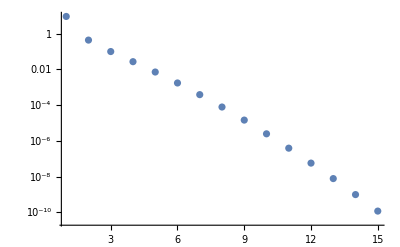

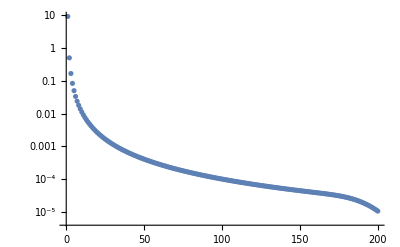

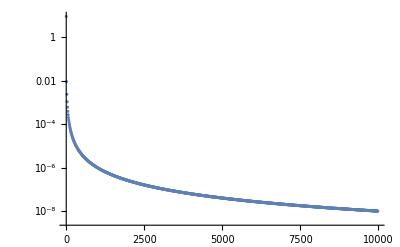

```mathematica
ListLogPlot[Table[{n,intvalue[n,10]},{n,1,15}],PlotRange->All]
ListLogPlot[Table[{n,intvalue[n,100]},{n,1,200}],PlotRange->All]
ListLogPlot[Table[{n,intvalue[n,1000]},{n,1,10000,10}],PlotRange->All]
```

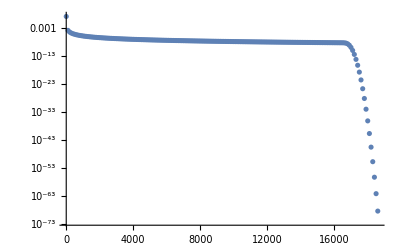

```mathematica
ListLogPlot[Table[{n,intvalue[n,1000]},{n,1,100000,100}],PlotRange->All]
```

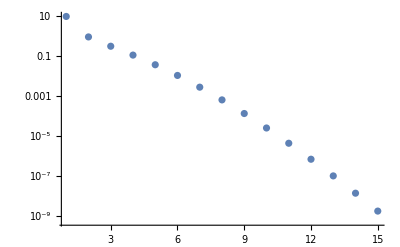

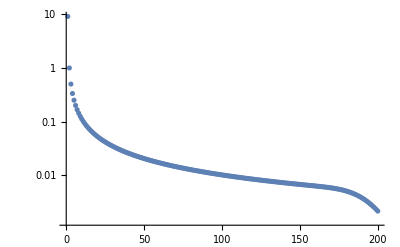

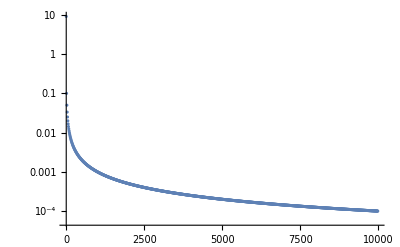

```mathematica
ListLogPlot[Table[{n,n intvalue[n,10]},{n,1,15}],PlotRange->All]
ListLogPlot[Table[{n,n intvalue[n,100]},{n,1,200}],PlotRange->All]
ListLogPlot[Table[{n,n intvalue[n,1000]},{n,1,10000,10}],PlotRange->All]
```

```mathematica
Table[Sum[n intvalue[n,1],{n,1,nmax}]//N,{nmax,{1,10,20,100}}]
```

{5.76864,5.78808,5.78808,5.78808}

```mathematica
Table[Sum[n intvalue[n,10],{n,1,nmax}]//N,{nmax,{1,10,20,100}}]
```

{9.08414,10.4005,10.4005,10.4005}

```mathematica
Table[Sum[n intvalue[n,100],{n,1,nmax}]//N,{nmax,{1,10,20,100,1000,10000}}]
```

{9.13318,11.9621,12.6809,14.3105,14.9888,14.9888}

```mathematica
Table[Sum[n intvalue[n,1000],{n,1,nmax}]//N,{nmax,{1,10,20,100,1000,10000,20000}}]

(*
Table[Sum[n intvalue[n,1000],{n,1,nmax}]//N,{nmax,{1,10,20,100,1000,10000,20000,100000}}]
-- result: --
{9.13,11.96,12.68,14.31,16.61,18.92,19.43,19.43}
*)
```

{9.13318,11.9621,12.6809,14.3105,16.6176,18.9206,19.4385}

```mathematica
(2π Z^2 α^2)/M(10)nion
```

```mathematica
Table[Log[((2M k^2/m^2)/(1+2k M/m^2+(M/m)^2))/((Z^2 α^2)/(b^2 M)/.b->((6π Z α ne)/Ef)^(-1/2))]//.{M->10^4,m->.5,Z->6,α->1/137.,ne->Z ni,ni->1,Ef->(3 π^2 ne)^(1/3)},{k,{10,100,1000}}]
```

{11.6793,16.2667,20.7094}

```mathematica
(Z^2 α^2)/(b^2 M)/.b->((6π Z α ne)/Ef)^(-1/2)//.{M->10^4,m->.5,Z->6,α->1/137.,ne->Z ni,ni->1,Ef->(3 π^2 ne)^(1/3)}
```

1.69×10^-7

```mathematica
1/b/.b->((6π Z α ne)/Ef)^(-1/2)/.ne->Ef^3/(3 π^2)
```

√(2/π) √(Ef^2 Z α)

```mathematica
1/b/.b->((6π Z α ne)/Ef)^(-1/2)//.{M->10^4,m->.5,Z->6,α->1/137.,ne->Z ni,ni->1,Ef->(3 π^2 ne)^(1/3)}
```

0.93867

```mathematica
((4α Ef √(Ef^2+m^2))/π)^(1/2)//.{M->10^4,m->.5,Z->6,α->1/137.,ne->Z ni,ni->1,Ef->(3 π^2 ne)^(1/3)}
```

0.54301

```mathematica
Table[Log[((2M k^2/m^2)/(1+2k M/m^2+(M/m)^2))/Max[(Z^2 α^2)/(b^2 M)/.b->((6π Z α ne)/Ef)^(-1/2),ωD]]//.{M->10^4,m->.5,Z->6,α->1/137.,ne->Z ni,ni->1,Ef->(3 π^2 ne)^(1/3),ωD->cs(6 π^2 ni)^(1/3),cs->0.01},{k,{10,100,1000}}]
```

{-0.669257,3.91811,8.36076}

```mathematica
intvalueScreened[n_,κInMeV_]:=Module[{},
(* must have   k - ω > Ef   =>   u < κ - Ef/ω0 *)
Return[If[u>κ-Ef/ω0//.{Ef->(3 π^3 ne)^(1/3),ne->Z ni,Z->6,ni->1},
0,
If[(u^2 ω0)/(2 M)<η2&&((2 κ-u)^2 ω0)/(2 M)>η2,
(Gamma[1+n,Q21]-Gamma[1+n,Q22])/(η2^2 n!)+(Gamma[-1+n,Q22]-Gamma[-1+n,Q23])/(n!)//.{Q21->(u^2 ω0)/(2 M),Q22->η2,Q23->((u-2 κ)^2 ω0)/(2 M),u->n},
If[(u^2 ω0)/(2M)>η2,(Gamma[-1+n,Q21]-Gamma[-1+n,Q22])/(n!)//.{Q21->(u^2 ω0)/(2 M),Q22->((u-2 κ)^2 ω0)/(2 M)},
"Invalid"]
]]/.{u->n,ω0->10^-2,M->10^4,η2->10^-4,κ->κInMeV/10^-2}]
];
```

```mathematica
Ef//.{Ef->(3 π^3 ne)^(1/3),ne->Z ni,Z->6,ni->1,ω0->10^-2}//N
```

8.2333

```mathematica
Table[κ-Ef/ω0//.{Ef->(3 π^3 ne)^(1/3),ne->Z ni,Z->6,ni->1,ω0->10^-2},{κ,{8.3/10^-2,10/10^-2,100/10^-2,1000/10^-2}}]//N
```

{6.66981,176.67,9176.67,99176.7}

```mathematica
intvalueScreened[3,10]
```

1/6 (Gamma[2,1/10000]-Gamma[2,3988009/2000000])+50000000/3 (Gamma[4,9/2000000]-Gamma[4,1/10000])

```mathematica
ListLogPlot[Table[{n,intvalueScreened[n,10]},{n,1,15}],PlotRange->All]
ListLogPlot[Table[{n,intvalueScreened[n,100]},{n,1,200}],PlotRange->All]
ListLogPlot[Table[{n,intvalueScreened[n,1000]},{n,1,10000,10}],PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Table[Sum[n intvalueScreened[n,8.3],{n,1,nmax}]//N,{nmax,{1,10,20,100}}]
```

{9.01267,10.0274,10.0274,10.0274}

```mathematica
Table[Sum[n intvalueScreened[n,10],{n,1,nmax}]//N,{nmax,{1,10,20,100}}]
```

{9.08414,10.4005,10.4005,10.4005}

```mathematica
Table[Sum[n intvalueScreened[n,100],{n,1,nmax}]//N,{nmax,{1,10,20,100,1000,10000}}]
```

{9.13318,11.9621,12.6809,14.3105,14.9888,14.9888}

```mathematica
Table[Sum[n intvalueScreened[n,1000],{n,1,nmax}]//N,{nmax,{1,10,20,100,1000,10000,20000}}]

(*
Table[Sum[n intvalue[n,1000],{n,1,nmax}]//N,{nmax,{1,10,20,100,1000,10000,20000,100000}}]
-- result: --
{9.13,11.96,12.68,14.31,16.61,18.92,19.43,19.43}
*)
```

{9.13318,11.9621,12.6809,14.3105,16.6176,18.9206,19.4385}

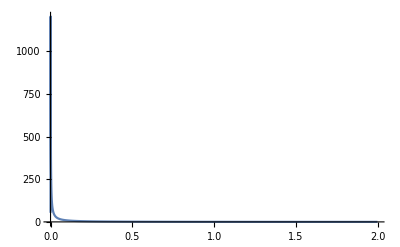
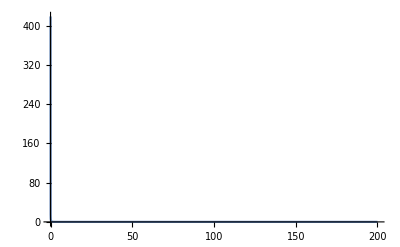
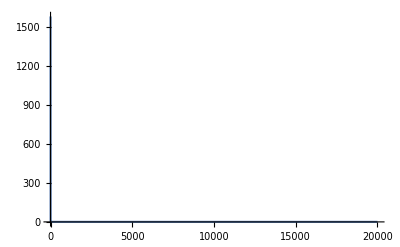

```mathematica
Table[Plot[Exp[-Q2]/(Q2+η2)^2 Q2/.η2->10^-4,{Q2,1/2(10^-6),((1-2 k/10^-2)^2)/2(10^-6)},PlotRange->All],{k,{10,100,1000}}]
```

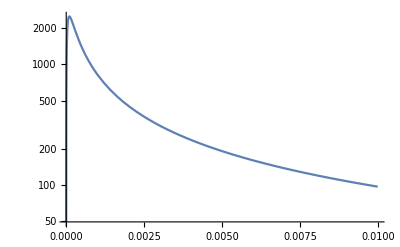
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[LogPlot[Exp[-Q2]/(Q2+η2)^2 Q2/.η2->10^-4,{Q2,1/2(10^-6),10^-2},PlotRange->All],{k,{10,100,1000}}]
```

```mathematica
intvalueScreened[1,10]//N
```

9.08414

```mathematica
Q2/(η2)^2(10η2)//.{Q2->η2,η2->10^-4}//N
```

10.

no screening

```mathematica
intvalueUnscreened[n_,κInMeV_]:=(Gamma[-1+n,Q21]-Gamma[-1+n,Q22])/(n!)//.{Q21->(u^2 ω0)/(2 M),Q22->((u-2 κ)^2 ω0)/(2 M)}/.{u->n,ω0->10^-6 M,η2->10^-4,κ->κInMeV/10^-2};
```

```mathematica
Table[Sum[n intvalueUnscreened[n,1],{n,1,nmax}]//N,{nmax,{1,10,20,100}}]
```

{10.5669,10.5864,10.5864,10.5864}

```mathematica
Table[Sum[n intvalueUnscreened[n,8.3],{n,1,nmax}]//N,{nmax,{1,10,20,100}}]
```

{13.8109,14.8263,14.8263,14.8263}

```mathematica
Table[Sum[n intvalueUnscreened[n,10],{n,1,nmax}]//N,{nmax,{1,10,20,100}}]
```

{13.8824,15.1988,15.1988,15.1988}

```mathematica
Table[Sum[n intvalueUnscreened[n,100],{n,1,nmax}]//N,{nmax,{1,10,20,100,1000,10000}}]
```

{13.9314,16.7604,17.4792,19.1088,19.7872,19.7872}

```mathematica
Table[Sum[n intvalueUnscreened[n,1000],{n,1,nmax}]//N,{nmax,{1,10,20,100,1000,10000,20000}}]

(*
Table[Sum[n intvalue[n,1000],{n,1,nmax}]//N,{nmax,{1,10,20,100,1000,10000,20000,100000}}]
-- result: --
{9.13,11.96,12.68,14.31,16.61,18.92,19.43,19.43}
*)
```

{13.9314,16.7604,17.4792,19.1088,21.4159,23.7189,24.2368}

## total cross section

```mathematica
Table[Sum[intvalueUnscreened[n,1],{n,1,nmax}]//N,{nmax,{1,10,20,100}}]
```

{10.5669,10.5766,10.5766,10.5766}

```mathematica
Table[Sum[intvalueUnscreened[n,10],{n,1,nmax}]//N,{nmax,{1,10,20,100}}]
```

{13.8824,14.4492,14.4492,14.4492}

```mathematica
Table[Sum[intvalueUnscreened[n,100],{n,1,nmax}]//N,{nmax,{1,10,20,100,1000,10000}}]
```

{13.9314,14.8314,14.8814,14.9214,14.9263,14.9263}

```mathematica
Table[Sum[intvalueUnscreened[n,1000],{n,1,nmax}]//N,{nmax,{1,10,20,100,1000,10000,20000}}]

(*
Table[Sum[n intvalue[n,1000],{n,1,nmax}]//N,{nmax,{1,10,20,100,1000,10000,20000,100000}}]
-- result: --
{9.13,11.96,12.68,14.31,16.61,18.92,19.43,19.43}
*)
```

{13.9314,14.8314,14.8814,14.9214,14.9304,14.9313,14.9314}

## spectrum 1-phonon calc

```mathematica
Exp[-q^2/(2m ωD)3/2](3 q^2 ω)/(2M ωD^3)
```

```mathematica
Exp[-Q^2 3/2](3 Q^2 ω)/ωD^2 HeavisideTheta[ωD-ω]
```

```mathematica
Exp[-Q^2] Q^2 DiracDelta[ω-ωD]
```

```mathematica
(2π Z^2 α^2 m^2)/(M k^2 ω0)Integrate[1/(Q2+η2)^2 Exp[-Q^2]Q2 δ(ω-ωD),{Q2,Q21,Q22}]
```

```mathematica
(2π Z^2 α^2 m^2)/(M k^2 ωD)Integrate[1/(Q2+η2)^2 Exp[-Q2 3/2](3Q2 ω)/ωD^2 HeavisideTheta[ωD-ω],{Q2,Q21,Q22}]
```

```mathematica
(2π Z^2 α^2 m^2)/(M k^2 ωD)((3ω)/ωD^2 HeavisideTheta[ωD-ω])Integrate[1/(Q2+η2)^2 Exp[-Q2 3/2]Q2,{Q2,Q21,Q22}]
```

```mathematica
Integrate[(3ω)/ω0^2 ω,{ω,0,ω0}]
```

ω0

```mathematica
intvalueSpectrum[u_,κInMeV_]:=If[(u^2 ω0)/(2 M)<η2&&((2 κ-u)^2 ω0)/(2 M)>η2,
(Gamma[1+n,Q21]-Gamma[1+n,Q22])/(η2^2 n!)+(Gamma[-1+n,Q22]-Gamma[-1+n,Q23])/(n!)//.{Q21->(u^2 ω0)/(2 M),Q22->η2,Q23->((u-2 κ)^2 ω0)/(2 M),u->n},
If[(u^2 ω0)/(2M)>η2,(Gamma[-1+n,Q21]-Gamma[-1+n,Q22])/(n!)//.{Q21->(u^2 ω0)/(2 M),Q22->((u-2 κ)^2 ω0)/(2 M)},
"Invalid"]
]/.{n->1,ω0->10^-6 M,η2->10^-4,κ->κInMeV/10^-2};
```

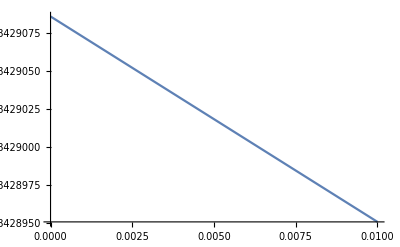

```mathematica
Plot[intvalueSpectrum[u,10],{u,0,10^-2}]
```

```mathematica
Integrate[Q2/(Q2+η2)^2,{Q2,0,Q2max},Assumptions->{Q2max>0,η2>0}]
```

-Q2max/(Q2max+η2)-Log[η2]+Log[Q2max+η2]

```mathematica
Log[Q2max/η2+1]-1
```

```mathematica
Integrate[(Q2 Exp[-Q2])/(Q2+η2)^2,{Q2,0,Q2max},Assumptions->{Q2max>0,η2>0}]
```

-1+(ⅇ^-Q2max η2)/(Q2max+η2)+ⅇ^η2 (1+η2) (-CoshIntegral[η2]+ExpIntegralEi[-Q2max-η2]+SinhIntegral[η2])

```mathematica
Integrate[(Q2^3 Exp[-Q2])/(Q2+η2)^2,{Q2,0,Q2max},Assumptions->{Q2max>0,η2>0}]
```

1/(Q2max+η2)ⅇ^-Q2max (-Q2max+ⅇ^Q2max Q2max-Q2max^2-η2+ⅇ^Q2max η2+Q2max η2-2 ⅇ^Q2max Q2max η2+2 η2^2-2 ⅇ^Q2max η2^2-ⅇ^Q2max Q2max η2^2+η2^3-ⅇ^Q2max η2^3+ⅇ^(Q2max+η2) η2^2 (3+η2) (Q2max+η2) ExpIntegralEi[-Q2max-η2]-ⅇ^(Q2max+η2) η2^2 (3+η2) (Q2max+η2) ExpIntegralEi[-η2])

```mathematica
Integrate[(Q2 Exp[-Q2])/(0+η2)^2,{Q2,0,η2},Assumptions->{Q2max>0,η2>0}]+Integrate[(Q2 Exp[-Q2])/(Q2+0)^2,{Q2,η2,Q2max},Assumptions->{Q2max>η2,η2>0}]
```

(1-ⅇ^-η2 (1+η2))/η2^2+ExpIntegralEi[-Q2max]-ExpIntegralEi[-η2]

```mathematica
(Gamma[1+n,Q21]-Gamma[1+n,Q22])/(η2^2 n!)+(Gamma[-1+n,Q22]-Gamma[-1+n,Q23])/(n!)//.{Q21->0,Q22->η2,Q23->Q2max,u->n,n->1}
```

-Gamma[0,Q2max]+Gamma[0,η2]+(1-Gamma[2,η2])/η2^2

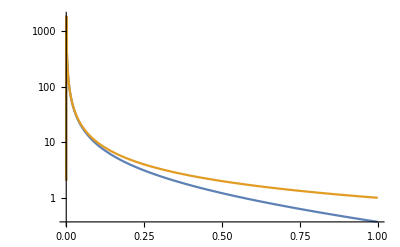

```mathematica
LogPlot[Evaluate[{(Q2 Exp[-Q2])/(Q2+η2)^2,Q2/(Q2+η2)^2}/.η2->10^-4],{Q2,0,1},PlotRange->All]
```

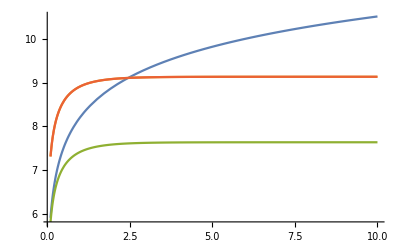

```mathematica
Plot[Evaluate[{
Log[Q2max/η2+1]-1,
-Gamma[0,Q2max]+Gamma[0,η2]+(1-Gamma[2,η2])/η2^2,
-1+(ⅇ^-Q2max η2)/(Q2max+η2)+ⅇ^η2 (1+η2) (-CoshIntegral[η2]+ExpIntegralEi[-Q2max-η2]+SinhIntegral[η2]),
(1-ⅇ^-η2 (1+η2))/η2^2+ExpIntegralEi[-Q2max]-ExpIntegralEi[-η2]}/.η2->10^-4],{Q2max,.1,10}]
```

```mathematica
Log[((2k)^2/(2M ω0))/(λ^2/(2M ω0))]
```

Log[(4 k^2)/λ^2]

```mathematica
{Log[(4 k^2)/λ2],intvalue[1,k]}/.{λ2->.3,k->10}//N
```

{7.19544,9.08414}

```mathematica
Log[((2M k^2/m^2)/(1+2k M/m^2+(M/m)^2))/((Z^2 α^2)/(b^2 M)/.b->((6π Z α ne)/Ef)^(-1/2))]
```

```mathematica
(2M k^2/m^2)/(M/m)^2
```

(2 k^2)/M

```mathematica
Log[((2 k^2)/M)/((Z^2 α^2)/(b^2 M))]
```

Log[(2 b^2 k^2)/(Z^2 α^2)]

```mathematica
(Z^2 α^2)/b^2//.{b->((6π Z α ne)/Ef)^(-1/2) ,λ->((4α Ef^2)/π)^(1/2),Ef->(3 π^2 ne)^(1/3),ne->Z ni,ω0->cs(3π ni)^(1/3),Z->6,α->1/137.,ni->1}(* is this ~ 1/λ^2 ? *)
```

0.00169

```mathematica
λ^2//.{b->((6π Z α ne)/Ef)^(-1/2) ,λ->((4α Ef^2)/π)^(1/2),Ef->(3 π^2 ne)^(1/3),ne->Z ni,ω0->cs(3π ni)^(1/3),Z->6,α->1/137.,ni->1,m->.5}
```

0.2937

```mathematica
2 3^(2/3) (ni/Z)^(2/3) π^(1/3) Z^3 α^3//FullSimplify[#,{ni>0,Z>0}]&
```

2 3^(2/3) ni^(2/3) π^(1/3) Z^(7/3) α^3

```mathematica
Z^2 α^2/.{Z->6,α->1/137.}
```

0.00191806

```mathematica
λ^2/(2 ω0^2)//.{λ->((4α Ef^2)/π)^(1/2),Ef->(3 π^2 ne)^(1/3),ni->ne/Z,ω0->cs(3π ni)^(1/3)}//FullSimplify[#,{ne>0,Z>0}]&
```

(2 Z^(2/3) α)/(cs^2 π^(1/3))

```mathematica
λ^2/(2 ω0^2)//.{λ->((4α Ef^2)/π)^(1/2),Ef->(3 π^2 ne)^(1/3),ni->ne/Z,ω0->(Z^2 α)/ni^(-1/3)}//FullSimplify[#,{ne>0,Z>0}]&
```

(2 3^(2/3) π^(1/3))/(Z^(10/3) α)

```mathematica
(Z^2 α^2)/(b^2 M)/.b->((6π Z α ne)/Ef)^(-1/2)//.{M->10^4,m->.5,Z->6,α->1/137.,ne->Z ni,ni->1,Ef->(3 π^2 ne)^(1/3)}
```

1.69×10^-7

```mathematica
1/b/.b->((6π Z α ne)/Ef)^(-1/2)/.ne->Ef^3/(3 π^2)
```

√(2/π) √(Ef^2 Z α)

```mathematica
1/b/.b->((6π Z α ne)/Ef)^(-1/2)//.{M->10^4,m->.5,Z->6,α->1/137.,ne->Z ni,ni->1,Ef->(3 π^2 ne)^(1/3)}
```

0.93867

```mathematica
((4α Ef √(Ef^2+m^2))/π)^(1/2)//.{M->10^4,m->.5,Z->6,α->1/137.,ne->Z ni,ni->1,Ef->(3 π^2 ne)^(1/3)}
```

0.54301